# IBM Rxn for Chemistry Retrosynthesis Evaluation

Will Borrelli

## IBM Rxn API Wrapper Code - (https://github.com/wrborrelli/IBMRxnAPI)

### Necessary Variable Assignments

```mathematica
(* Initial run of this notebook will prompt you to enter your authorization key. Once you've done that feel free to delete the following cell. *)
```

```mathematica
(*SystemCredential["authKey"]=InputString["Authorization Key"];*)
```

```mathematica
authKey=SystemCredential["authKey"];
```

### Wrapper Code

```mathematica
baseURL="rxn.res.ibm.com";
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
]]
```

```mathematica
(* duplicate of above - for adding a output format parameter *)
```

```mathematica
IBMRxn[req_String,molecs_List,projID_String,outType_String]:=Module[
{reactantList={},createProj,projectID,createPred,getPred,rxnImg,rxnConf,predID,projName,reactants,rsmiles},

If[(* If[] you want to make a "new prediction", this code block runs *)
req=="new prediction",
Do[
Which[
ImageQ[molecs[[i]]],
AppendTo[reactantList,MoleculeRecognize[molecs[[i]]]["SMILES"]]
,
StringQ[molecs[[i]]],
AppendTo[reactantList,molecs[[i]]]
],{i,1,Length[molecs]}];

reactants=ToString[Row[#,"."]&@reactantList];
createPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/pr?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
predID=createPred["payload","id"];

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projectID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projectID=getPred["payload","attempts"][[1]]["projectId"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projectID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
]]
```

```mathematica
(* for getting more outcomes from a prediction that you've already made *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
]]
```

```mathematica
(* duplicate of above - for adding an output type *)
```

```mathematica
IBMRxn[req_String,projID_String,predID_String,outType_String]:=Module[
{getPred,reactants,morePreds,projName,rxnImgList={},rxnConfList={},rsmilesList={},rxnImages,rxnTables,preds},

If[req=="more predictions",
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
reactants=getPred["payload","request","reactants"];

Pause[10];

morePreds=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/prb?predictionId="<>predID<>"&projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"reactants"->reactants|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;

Pause[10];

getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>predID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

Which[
outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];


rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;
rxnTables=TableForm[{{projName,projID,predID,#}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]&/@rxnConfList;

preds=Partition[Riffle[rxnImages,rxnTables],2];
preds
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];

Do[(* add each rxn img to the list *)
AppendTo[rxnImgList,getPred["payload","attempts"][[i]]["reactionImage"]],
{i,1,Length[getPred["payload","attempts"]]}];
	Do[(* add each confidence to the list *)
AppendTo[rxnConfList,getPred["payload","attempts"][[i]]["confidence"]],
{i,1,Length[getPred["payload","attempts"]]}];
Do[(* add each rsmiles to the list *)
AppendTo[rsmilesList,getPred["payload","attempts"][[i]]["smiles"]],
{i,1,Length[getPred["payload","attempts"]]}];

rxnImages=ResourceFunction["SVGImport"][#]&/@rxnImgList;

Dataset@MapThread[<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[#1][[1]],"rprod"->reacSplit[#1][[2]],"conf"->#2,"reaction image"->#3|>&,{rsmilesList,rxnConfList,rxnImages}]
]
]]
```

```mathematica
(* for making a new retrosynthesis *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100]},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->"",
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];

retImg
retTable
]]
```

```mathematica
(* duplicate of above - added to specify a precursor *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* duplicate of above - added to specify output type *)
```

```mathematica
IBMRxn[req_String,projID_String,prod_List,prec_String,outType_String]:=Module[
{prodSMILE,createRet,retID,getRet,seqMolecList,seqSMILES,molecPlots,stepsImgs,stepDescs,retTable,retConf,retOptScore,retImg,rClass,seqConf,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],out,seqs,childsNumb,cImgs,childs,product,cols,cSMILES,retroID},

If[(* this code block runs to make and get a new retrosynthesis *)
req=="new retrosynthesis",
Which[
ImageQ[prod[[1]]],
prodSMILE=MoleculeRecognize[prod[[1]]]["SMILES"],
StringQ[prod[[1]]],
prodSMILE=prod[[1]]
];

createRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/rs?projectId="<>projID],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|
"isInteractive"->"false",
"parameters"-><|"availability_pricing_threshold"->0,
"available_smiles"->prec,
"exclude_smiles"->"",
"exclude_substructures"->"",
"exclude_target_molecule"->"true",
"fap"->0,
"max_steps"->0,
"nbeams"->0,
"pruning_steps"->0|>,
"product"->prodSMILE
|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
retID=createRet["payload","id"];

Pause[10];

getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
While[(* Loops until the get request says the task status is "DONE" *)
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>retID],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILE]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{product,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retTable=TableForm[{{projID,retID,retConf,retOptScore,rClass,seqConf}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class","Sequence Confidence"}}];*)
]]
```

```mathematica
(* for making a new project, listing all project attempts, or recovering a past prediction or retrosynthesis *)
```

```mathematica
IBMRxn[req_String,IDorName_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* duplicate of above - added to allow for specifying ouput type *)
```

```mathematica
IBMRxn[req_String,IDorName_String,outType_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,allProjAs,getPred,projName,rxnImg,rxnConf,predID,projID,createProj,projectID,getRet,seqMolecList,seqSMILES,retConf,retOptScore,molecPlots,retTable,stepsImgs,arrow=Graphics[Text@Style["⇒",60],BaselinePosition->Center,ImageSize->100],stepDescs,retImg,prodSMILES,rClass,seqConf,seqs,prod,childsNumb,out,cImgs,childs,retroID,product,cols,cSMILES,rsmiles},

Which[
req=="new project",(* for a "new project", following code block runs *)
createProj=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"POST",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>,
"Body"->ExportString[<|"name"->ToString[IDorName],"invitations"->{}|>,"JSON"]|>]//URLExecute[#,"RawJSON"]&;
projectID=createProj["payload","id"];
TableForm[{{IDorName,projectID}},TableHeadings->{None,{"Project Name","Project ID"}}]
,
req== "all project attempts",(* for getting "all project attempts", following code block runs *)
allProjAs=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects/"<>IDorName<>"/attempts?raw={}"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;
allProjAs,
req=="recover prediction",(* to "recover prediction", following code block runs *)
getPred=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/predictions/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;
Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];

rxnImg
TableForm[{{projName,projID,predID,rxnConf}},TableHeadings->{None,{"Project Name","Project ID","Prediction ID","Prediction Confidence"}}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
projName=StringReplace[getPred["payload","attempts"][[1]]["name"],"_"~~___->""];
projID=getPred["payload","attempts"][[1]]["projectId"];
predID=getPred["payload","id"];
rxnImg=ResourceFunction["SVGImport"][getPred["payload","attempts"][[1]]["reactionImage"]];
rxnConf=getPred["payload","attempts"][[1]]["confidence"];
rsmiles=getPred["payload","attempts"][[1]]["smiles"];

<|"project name"->projName,"projID"->projID,"predID"->predID,"rreac"->reacSplit[rsmiles][[1]],"rprod"->reacSplit[rsmiles][[2]],"conf"->rxnConf,"reaction image"->rxnImg|>//Dataset
]
,
req=="recover retrosynthesis",(* recover a previously made retrosynthesis *)
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

While[
getRet["payload","task","status"]≠"DONE",
Pause[10];
getRet=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/"<>IDorName],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>|>]//URLExecute[#,"RawJSON"]&;

];
projID=getRet["payload","projectId"];

(*retConf=getRet["payload","sequences"][[1]]["confidence"];
seqConf=getRet["payload","siblings"][[-1]]["reactions"][[1]]["confidence"];
retOptScore=getRet["payload","sequences"][[1]]["optimizationScore"];

prodSMILES=getRet["payload","wizardParameters","exclude_smiles"][[1]];
molecPlots=MoleculePlot[Molecule[StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]],ImageSize->Large];
rClass=getRet["payload","siblings"][[-1]]["reactions"][[1]]["rclass"];

retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)

Which[outType==""||StringMatchQ[ToString@outType,"default",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

retImg=Table[
prod=getRet["payload","sequences"][[i]]["tree","smiles"]//Molecule//MoleculePlot;
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cImgs=Map[MoleculePlot[#]&,Molecule[#]&/@Flatten@Rest@out];

retImg=GraphicsRow[{prod,arrow,cImgs},ImageSize->Full];
retTable=TableForm[{{projID,IDorName,retConf,retOptScore,rClass}},TableHeadings->{None,{"Project ID","Retrosynthesis ID","Retrosynthesis Confidence","Retrosynthesis Optimization Score","Reaction Class"}}];

Column[{retImg,retTable}]
,{i,1,seqs}]
,
StringMatchQ[ToString@outType,"dataset",IgnoreCase->True],
seqs=Length@getRet["payload","sequences"];

cols=Table[
product=getRet["payload","sequences"][[i]]["tree","smiles"];
retroID=getRet["payload","sequences"][[1]]["retrosynthesisId"];
rClass=getRet["payload","sequences"][[i]]["tree","rclass"];
retOptScore=getRet["payload","sequences"][[i]]["optimizationScore"];
retConf=getRet["payload","sequences"][[i]]["confidence"];
childsNumb=getRet["payload","sequences"][[i]]["tree","children"]//Length;
out=Reap[Do[
childs=getRet["payload","sequences"][[i]]["tree","children"][[n]]["smiles"];
Sow[childs];
,{n,1,childsNumb}]];
cSMILES=Flatten@Rest@out;

{rClass,projID,retroID,cSMILES,product,retConf,retOptScore}
,{i,1,seqs}];
MapThread[<|"rclass"->#1,"projID"->#2,"retroID"->#3,"rreac"->StringRiffle[#4,"."],"prod"->#5,"conf"->#6,"opt"->#7|>&,{cols[[All,1]],cols[[All,2]],cols[[All,3]],cols[[All,4]],cols[[All,5]],cols[[All,6]],cols[[All,7]]}]//Dataset
]

(*retImg=GraphicsRow[{MoleculePlot[Molecule[prodSMILES]],arrow,StringReplace[getRet["payload","siblings"][[-1]]["reactions"][[1]]["smiles"],"~"->"."]//Molecule//MoleculePlot}];*)
]]
```

```mathematica
(* just for getting all stored projects. if "stored projects" is given as input, outputs a dataset of all stored projects as well as the total number of projects stored *)
```

```mathematica
IBMRxn[req_String]:=Module[
{myProjects,myProjNames,myProjIDs,nameRule,idRule,myProjectsData,queueState},
Which[(* If[] you want to get all "stored projects", this code block runs *)
req=="stored projects",
myProjects=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/projects"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

myProjNames=#["name"]&/@myProjects["payload","content"];
myProjIDs=#["id"]&/@myProjects["payload","content"];

nameRule=("Project Name"->#&/@myProjNames);
idRule=("Project ID"->#&/@myProjIDs);

myProjectsData=
Dataset[
Association[#]&/@Transpose[{nameRule,idRule}]]
TableForm[{{ToString[myProjects["payload","totalElements"]]}},TableHeadings->{None,{"Total Stored Projects"}},TableAlignments->Center]
,
req=="queue status",(* get the status of the retrosynthesis queue *)
queueState=HTTPRequest[URL[baseURL<>"/rxn/api/api/v1/retrosynthesis/queue-state"],
<|"Method"->"GET",
"Headers"-><|"Content-Type"->"application/json",
"Authorization"->authKey|>
|>]//URLExecute[#,"RawJSON"]&;

queueState
]]
```

## Helper Functions

```mathematica
pcComp[molec_String]:=First[ServiceExecute["PubChem","CompoundProperties",{"SMILES"->molec,"Property"->"Complexity"}]]["Complexity"]
```

```mathematica
SetAttributes[pcComp,Listable]
```

```mathematica
SetAttributes[compDiffPC,Listable]
```

```mathematica
compDiffPC[rSmiles_String]:=Module[{reactants,product,rComp,pComp},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
product=StringSplit[reacSplit[rSmiles][[2]],"."];

rComp=Total[pcComp[reactants]];
pComp=Total[pcComp[product]];
pComp-rComp
]
```

```mathematica
compDiff[rSmiles_String]:=Module[{reactants,prod,rComp,pComp},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
prod=StringSplit[reacSplit[rSmiles][[2]],"."];

rComp=Total@Table[If[SameQ[Head[Quiet@MolecularComplexity[reactants[[i]]]],Real],MolecularComplexity[reactants[[i]]],0],{i,1,Length@reactants}];
pComp=Total@Table[If[SameQ[Head[Quiet@MolecularComplexity[prod[[i]]]],Real],MolecularComplexity[prod[[i]]],0],{i,1,Length@prod}];

pComp-rComp
]
```

```mathematica
(* builds dataset from csv of {rnumber,tclass,rsmiles,notes} -> {reaction number,true class,rsmiles,true reactants,product,tComplexity Difference,crsmiles,ctreac,cprod,notes} *)
```

```mathematica
makeDat[dat_]:=Module[{reactants,prod},
dat[All,<|"reaction number"->#rnumber,"true rclass"->#tclass,"rsmiles"->#rsmiles,"treacs"->reacSplit[#rsmiles][[1]],"tprod"->reacSplit[#rsmiles][[2]],
"true complexity difference"->
(
compDiff[#rsmiles]
)
,
"canonical rsmiles"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]<>">>"<>Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,
"canonical treacs"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]
)
,
"canonical tprod"->
(
Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,"notes"->#notes|>&]
]
```

```mathematica
makeDatNoCm[dat_]:=Module[{reactants,prod},
dat[All,<|"reaction number"->#rnumber,"true rclass"->#tclass,"rsmiles"->#rsmiles,"treacs"->reacSplit[#rsmiles][[1]],"tprod"->reacSplit[#rsmiles][[2]]
,
"canonical rsmiles"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]<>">>"<>Molecule[reacSplit[#rsmiles][[2]]]["CanonicalSMILES"]
)
,
"canonical treacs"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]
)
,
"canonical tprod"->
(
Molecule[reacSplit[#rsmiles][[2]]]["CanonicalSMILES"]
)
,"notes"->#notes|>&]
]
```

```mathematica
(* same as above but uses PubChem complexity *)
```

```mathematica
makeDatPC[dat_]:=Module[{reactants,prod},
dat[All,<|"reaction number"->#rnumber,"true rclass"->#tclass,"rsmiles"->#rsmiles,"treacs"->reacSplit[#rsmiles][[1]],"tprod"->reacSplit[#rsmiles][[2]],
"true complexity difference"->
(
If[
FailureQ[compDiffPC[#rsmiles]]||Head[compDiffPC[#rsmiles]]==Missing,"Failed",compDiffPC[#rsmiles]
]
)
,
"canonical rsmiles"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]<>">>"<>Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,
"canonical treacs"->
(
reactants=StringSplit[reacSplit[#rsmiles][[1]],"."];
StringRiffle[Table[Molecule[reactants[[i]]]["CanonicalSMILES"],{i,1,Length@reactants}],"."]
)
,
"canonical tprod"->
(
Molecule[reacSplit[#rsmiles][[1]]]["CanonicalSMILES"]
)
,"notes"->#notes|>&]
]
```

```mathematica
(* following two from Mathematica Topological Similarity Searching:(https://www.wolfram.com/language/12/molecular-structure-and-computation/topological-similarity-searching.html.en?footer=lang)
```

```mathematica
atomPairs[mol_]:=atomPairs[mol]=Module[{distMat,pairIndices,atomData,atomPair,counts,reorder},atomData=AtomList[mol,_,{"AtomicSymbol","PiElectronCount","HeavyAtomCoordinationNumber"}];
distMat=MoleculeValue[mol,"GraphDistanceMatrix"];
pairIndices=Subsets[AtomList[mol,Except@"H","AtomIndex"],{2}];
atomPair=Function[{i,j},Sort@{atomData[[i]],distMat[[i,j]],atomData[[j]]}];
Counts[atomPair@@@pairIndices]]
```

```mathematica
apDistance[pairVector1_,pairVector2_]:=
Module[{A,B,AandB},A=Total[pairVector1];
B=Total[pairVector2];
AandB=Total[Merge[KeyIntersection[{pairVector1,pairVector2}],Min]];
1-((2*AandB)/(A+B))];
moleculeDistance[mol1_,mol2_]:=
N[apDistance[atomPairs[mol1],atomPairs[mol2]]]
```

```mathematica
(* computes the topological or fingerprint similarity of the true and predictive reactants to the product *)
```

```mathematica
cSim[dat_,simMethod_String]:=Module[
{prod=Molecule@Normal@dat["prod"],treac=Molecule[#]&/@StringSplit[Normal@dat["treac"],"."],rreac=Molecule[#]&/@StringSplit[Normal@dat["rreac"],"."],treacSim,rreacSim},

Which[
StringMatchQ[ToString@simMethod,"topological",IgnoreCase->True],

treacSim=Total@Table[moleculeDistance[prod,treac[[i]]],{i,1,Length@treac}];
rreacSim=Total@Table[moleculeDistance[prod,rreac[[i]]],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>,

StringMatchQ[ToString@simMethod,"fingerprint",IgnoreCase->True]||StringMatchQ[ToString@simMethod,"fp",IgnoreCase->True],

treacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,treac[[i]]],{i,1,Length@treac}];
rreacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,rreac[[i]]],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>
]
]
```

```mathematica
(* duplicate of above - adds option for specifying fp type and similarity measure *)
```

```mathematica
cSim[dat_,simMethod_String,fpType_String,simMeas_String]:=Module[
{prod=Molecule@Normal@dat["prod"],treac=Molecule[#]&/@StringSplit[Normal@dat["treac"],"."],rreac=Molecule[#]&/@StringSplit[Normal@dat["rreac"],"."],treacSim,rreacSim},

Which[
StringMatchQ[ToString@simMethod,"topological",IgnoreCase->True],

treacSim=Total@Table[moleculeDistance[prod,treac[[i]]],{i,1,Length@treac}];
rreacSim=Total@Table[moleculeDistance[prod,rreac[[i]]],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>,

StringMatchQ[ToString@simMethod,"fingerprint",IgnoreCase->True]||StringMatchQ[ToString@simMethod,"fp",IgnoreCase->True],

treacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,treac[[i]],"FingerprintType"->fpType,"SimilarityMeasure"->simMeas],{i,1,Length@treac}];
rreacSim=Total@Table[ResourceFunction["MoleculeFingerprintSimilarity"][prod,rreac[[i]],"FingerprintType"->fpType,"SimilarityMeasure"->simMeas],{i,1,Length@rreac}];
<|"treac similarity"->treacSim,"rreac similarity"->rreacSim|>
]
]
```

```mathematica
(* Molecular complexity calculation *)
```

```mathematica
MolecularComplexity[mol_]:=Module[{molec=Molecule[mol],aInds,aSyms,indTsym,symAtoms,symAtomsNoH,symAtomsNoHv1,indTval,indTcon,bondPairs,bondIndPairs,bondIndsNoH,bondIndPairsNoH,ind,jnd,atomI,vi,bi,di,dj,bondedAs,ei,eAs,si,vj,bj,sj,ej,out,terms,atomII,atomIIpos,jnds,nonEqTerms,eqTerms,allTerms,bTypes,sharedA,adjA,aIndsNoH,adjM},
aInds=MoleculeValue[molec,"AtomIndex"];(*  atom indices *)
aIndsNoH=Select[Thread[{MoleculeValue[molec,"AtomicSymbol"],aInds}],Not@MemberQ[#,"H"]&][[All,2]];
aSyms=MoleculeValue[molec,"AtomicSymbol"];
indTsym=AssociationThread[aInds,aSyms];(* atom indicex -> atomic symbol *)
symAtoms=MoleculeValue[molec,"SymmetryEquivalentAtoms"];
adjM=Normal[MoleculeValue[molec,"AdjacencyMatrix"]];
symAtomsNoHv1=Select[Thread[{TakeList[aSyms,Length[#]&/@symAtoms],symAtoms}],Not@MemberQ[#[[1]],"H"]&][[All,2]];
symAtomsNoH=Table[(* I'm kind of unsure about this fix, maybe it works? *)
Which[
Length[m]==1,{m},
Length[m]>1,
sharedA=First@Position[First[Intersection[adjM[[m,aIndsNoH]]]],1];(* gets the atom that the sym atoms share *)
adjA=First@Position[First[adjM[[sharedA,aIndsNoH]]]*Boole[Not@ContainsAny[m,{#}]&/@Range[Length@aIndsNoH]],1];(* gets the atoms that the shared atom is bonded to *)
If[ContainsOnly[Flatten[Position[First[adjM[[sharedA,aIndsNoH]]],1]],m],{m},
If[SameQ[First@Table[MoleculeValue[molec,{"AtomChirality",j}],{j,adjA}],None],{m},Split[m]]
](* tests if those attached atoms are stereocenters *)
]
,{m,symAtomsNoHv1}]//Flatten[#,1]&//Quiet;(* lists of symmetrically equivalent atoms *)
indTval=AssociationThread[MoleculeValue[molec,"AtomIndex"],MoleculeValue[molec,"OuterShellElectronCount"]];(* atom index -> valence *)
bondPairs=Lookup[indTsym,#]&/@MoleculeValue[molec,"BondedAtomIndices"];(* list of lists of bonded atom indices *)
bondIndPairs=Thread[{bondPairs,MoleculeValue[molec,"BondedAtomIndices"]}];(* list of pairs of {bonded atom symbols, bonded atom indices} *)
bondIndsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&][[All,2]]; (* list of lists of bonded indices with H removed *)
bondIndPairsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&]; 


terms=Table[
atomI=symAtomsNoH[[i]];
If[Length[atomI]==1,(* if there are no equivalent atoms *)

vi=indTval[First[atomI]];
bi=(
bTypes=MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]];
Total[
Which[
indTsym[First[atomI]]=="C",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],

indTsym[First[atomI]]=="O"||indTsym[First[atomI]]=="S",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->1}],

indTsym[First[atomI]]=="N",
Which[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==3),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]==1),
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==2),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]],

True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]]
]
);
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

{di,ei,si,vi,bi}
,(* if there is more than 1 equivalent atom *)
vi=indTval[First[atomI]];
bi=(
bTypes=MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]];
Total[
Which[
indTsym[First[atomI]]=="C",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],

indTsym[First[atomI]]=="O"||indTsym[First[atomI]]=="S",
If[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&Counts[bTypes]["Aromatic"]>1,Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->1}],

indTsym[First[atomI]]=="N",
Which[MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==3),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->1,"Double"->2,"Triple"->3},
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]==1),
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}],
MemberQ[Keys[Counts[bTypes]],"Aromatic"]&&(Counts[bTypes]["Aromatic"]>1)&&(Length[Select[Flatten[Select[bondIndPairs,MemberQ[#[[2]],First[atomI]]&][[All,2]]],#≠First[atomI]&]]==2),Join[DeleteDuplicates[bTypes],{"Single"}]/.{"Single"->1,"Aromatic"->2,"Double"->2,"Triple"->3},True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]],

True,
Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}]]
]
);
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

Table[{di,ei,si,vi,bi},Length@atomI]
],{i,1,Length@symAtomsNoH}];

nonEqTerms=Select[terms,Not[MatrixQ[#]]&];
eqTerms=Flatten[Select[terms,MatrixQ[#]&],1];
allTerms=Join[nonEqTerms,eqTerms];

If[Length[eqTerms]>0,
N[Sum[(
allTerms[[All,1]][[s1]]*allTerms[[All,2]][[s1]]*allTerms[[All,3]][[s1]]*Log2[(allTerms[[All,4]][[s1]]*allTerms[[All,5]][[s1]])])
,{s1,1,Length@allTerms}]-0.5*Sum[(eqTerms[[All,1]][[j1]]*eqTerms[[All,2]][[j1]]*eqTerms[[All,3]][[j1]]*Log2[(eqTerms[[All,4]][[j1]]*eqTerms[[All,5]][[j1]])]),{j1,1,Length@eqTerms}]]
,
N[Sum[
allTerms[[All,1]][[s2]]*allTerms[[All,2]][[s2]]*allTerms[[All,3]][[s2]]*Log2[allTerms[[All,4]][[s2]]*allTerms[[All,5]][[s2]]]
,{s2,1,Length@allTerms}]]
]
]
```

```mathematica
SetAttributes[MolecularComplexity,Listable]
```

```mathematica
prodSel[dat_Dataset,prod_String]:=dat[Select[#prod==prod&]]
```

```mathematica
cSmiles[smiles_]:=smiles[[1]]<>"."<>smiles[[2]]
```

```mathematica
reacSplit[reacs_String]:=StringSplit[reacs,">>"];
```

## Initial Test Set and Results Data

```mathematica
(* load in our dataset containing the smiles for selected reactions *)
```

```mathematica
iRtDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reactions\\retro-test.xlsx",HeaderLines->1];
```

```mathematica
iResDat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\retro_results.csv"][[All,{"tclass","rclass","projId","retroId","treac","rreac","prod","conf"}]];
```

```mathematica
iTsDat=Dataset@
Flatten[Normal[Import["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reactions\\test-set.xlsx","Dataset",HeaderLines->1]],1];
```

```mathematica
retDat=makeDatNoCm@SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\reactions\\WOS_Rxns.xlsx"];
```

```mathematica
iTsDatFormatted=makeDatNoCm[Dataset[<|"rnumber"->"","tclass"->#[[1]],"rsmiles"->#[[2]],"notes"->""|>&/@Flatten[Table[{Normal[Keys[First[iTsDat]]][[i]],#}&/@Normal[Transpose[iTsDat]][[i]],{i,1,Length@Normal[Keys[First[iTsDat]]]}],1]]];
```

```mathematica
(* iTsDatFormatted has some rxns with multiple products, take only ones with 1 product and join with retDat *)
```

```mathematica
allRetDat=Join[retDat,iTsDatFormatted[Select[Length[StringSplit[reacSplit[#rsmiles][[2]],"."]]==1&]]];
```

```mathematica
Table[<|i->Length@allRetDat[Select[#"true rclass"==i&]]|>,{i,DeleteDuplicates[Normal[allRetDat[[All,"true rclass"]]]]}]
```

{<|substitution→9|>,<|friedelcrafts→11|>,<|electrophilic aromatic substitution→1|>,<|nucleophilic aromatic substitution→3|>,<|amide formation→1|>,<|cyclisation→3|>,<|epoxide opening→1|>,<|conjugate addition→1|>,<|dielsalder→11|>,<|elimination→4|>,<|grignard→10|>,<|organocopper→9|>,<|acetylide→9|>,<|e-sub→9|>,<|robinson→10|>,<|amine→9|>}

```mathematica
(* add project IDs for each reaction class *)
```

```mathematica
rclassTpID=Association@{<|"conjugate addition"->"5f3aca785ce6d3000172161a"|>,<|"epoxide opening"->"5f3aca5b5ce6d30001721613"|>,<|"cyclisation"->"5f3aca345ce6d3000172160b"|>,<|"electrophilic aromatic substitution"->"5f3d47c43dc67c0001c326fc"|>,<|"nucleophilic aromatic substitution"->"5f3ac7245ce6d30001721576"|>,<|"amide formation"->"5f3ac7365ce6d3000172157d"|>,<|"substitution"->"5f3ac7475ce6d30001721584"|>,<|"elimination"->"5f3ac7515ce6d30001721587"|>,<|"grignard"->"5f3ac75a5ce6d3000172158a"|>,<|"organocopper"->"5f3ac7625ce6d3000172158f"|>,<|"friedelcrafts"->"5f3ac76e5ce6d30001721594"|>,<|"dielsalder"->"5f3ac7785ce6d30001721597"|>,<|"acetylide"->"5f3ac78d5ce6d3000172159e"|>,<|"e-sub"->"5f3ac7995ce6d300017215a1"|>,<|"robinson"->"5f3ac7a65ce6d300017215a8"|>,<|"amine"->"5f3ac7ad5ce6d300017215ab"|>};
```

```mathematica
allRetDat=allRetDat[All,<|"reaction number"->#"reaction number","true rclass"->#"true rclass","rsmiles"->#rsmiles,"treacs"->#treacs,"tprod"->#tprod,"canonical rsmiles"->#"canonical rsmiles","canonical treacs"->#"canonical treacs","canonical tprod"->#"canonical tprod","project ID"->rclassTpID[#"true rclass"],"notes"->#notes|>&];
```

## Get More Retrosynthesis Results

```mathematica
Clear[testRet]
```

```mathematica
testRet[dat_]:=Module[{projectID=dat["project ID"],retPreds,t5RetPreds,rreac,rprod,rrsmiles,retID,retConf,retOpt,rrclass,fPred,fPredID,frreac,frprod,frrsmiles,fConf,cretPreds,ct5RetPreds,crreac,crprod,crrsmiles,cretID,cretConf,cretOpt,crrclass,canSame},
(* make retro run, get dataset of sequences *)
retPreds=IBMRxn["new retrosynthesis",projectID,{dat["tprod"]},"","dataset"];

(* get ret info *)
t5RetPreds=Take[retPreds[ReverseSortBy[#conf&]],1];
rreac=Normal@First[Take[retPreds[ReverseSortBy[#conf&]],1]]["rreac"];
rprod=Normal@First[Take[retPreds[ReverseSortBy[#conf&]],1]]["prod"];
rrsmiles=ToString[rreac<>">>"<>rprod];
retID=Normal@First[Take[retPreds[ReverseSortBy[#conf&]],1]]["retroID"];
retConf=Normal@First[Take[retPreds[ReverseSortBy[#conf&]],1]]["conf"];
retOpt=Normal@First[Take[retPreds[ReverseSortBy[#conf&]],1]]["opt"];
rrclass=Normal@First[Take[retPreds[ReverseSortBy[#conf&]],1]]["rclass"];

Pause[3];

(* Get the forward prediction *)
fPred=IBMRxn["new prediction",StringSplit[dat["treacs"],"."],projectID,"dataset"];

(* get forward pred info*)
fPredID=fPred["predID"];
frreac=fPred["rreac"];
frprod=fPred["rprod"];
frrsmiles=StringRiffle[{fPred["rreac"],fPred["rprod"]},">>"];
fConf=fPred["conf"];

Pause[10];

(* Test if canonical SMILES gives the same results - make ret request *)
cretPreds=IBMRxn["new retrosynthesis",projectID,{dat["canonical tprod"]},"","dataset"];

(* get canonical ret info *)
ct5RetPreds=Take[cretPreds[ReverseSortBy[#conf&]],1];
crreac=Normal@First[Take[cretPreds[ReverseSortBy[#conf&]],1]]["rreac"];
crprod=Normal@First[Take[cretPreds[ReverseSortBy[#conf&]],1]]["prod"];
crrsmiles=ToString[crreac<>">>"<>crprod];
cretID=Normal@First[Take[cretPreds[ReverseSortBy[#conf&]],1]]["retroID"];
cretConf=Normal@First[Take[cretPreds[ReverseSortBy[#conf&]],1]]["conf"];
cretOpt=Normal@First[Take[cretPreds[ReverseSortBy[#conf&]],1]]["opt"];
crrclass=Normal@First[Take[cretPreds[ReverseSortBy[#conf&]],1]]["rclass"];
(* is non-canonical and canonical the same? - maybe a problem? *)
(*canSame*)

Dataset[<|"reaction number"->dat["reaction number"],
"true rclass"->dat["true rclass"],"true rsmiles"->dat["rsmiles"],"true reacs"->dat["treacs"],"true prod"->dat["tprod"],"notes"->dat["notes"],

"canonical true rsmiles"->dat["canonical rsmiles"],"canonical true reacs"->dat["canonical treacs"],"canonical true prod"->dat["canonical tprod"],

"project ID"->dat["project ID"],

"ret ID"->retID,"ret pred rclass"->rrclass,"ret pred rsmiles"->rrsmiles,"ret pred reacs"->rreac,"ret confidence"->retConf,"ret optimization"->retOpt,

"canonical ret ID"->cretID,"canonical ret pred rsmiles"->crrsmiles,"canonical ret pred reacs"->crreac,"canonical ret confidence"->cretConf,"canonical ret optimization"->cretOpt,

"forward pred ID"->fPredID,"forward pred rsmiles"->frrsmiles,"forward pred reacs"->frreac,"forward pred prod"->frprod,"forward pred confidence"->fConf
|>]
]
```

```mathematica
(* one of the acetylide reactions was a typo, so another diels alder was added *)
```

```mathematica
(* we can get the results for the single reaction samples as follows, this was repeated for all single reactions *)
```

```mathematica
(*retDatEAS=testRet[First[allRetDat[Select[#"true rclass"=="electrophilic aromatic substitution"&]]]];
```

```mathematica
(* get the multi-rxn api requests *)
```

```mathematica
bGetRet[rxns_Dataset]:=Module[{out},
Dataset[Table[
out=Normal[testRet[rxns[[i]]]];
Pause[60];
out
,{i,1,Length@rxns}]]
]
```

```mathematica
(* This was repeated for each reaction class group *)
```

```mathematica
(*retDatCyc=bGetRet[allRetDat[Select[#"true rclass"=="cyclisation"&]]];
```

```mathematica
(* thus far only 98 will run, with the last 2 robinson rxns failing *)
```

```mathematica
(* Here is our data: *)
```

```mathematica
allDatAPI98=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\retDat98.csv"];
```

## Data Processing

```mathematica
(* for computing the difference in synthetic accessiblity score *)
```

```mathematica
dSA[rSmiles_String]:=Module[{reactants,products,rSA,pSA},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
products=StringSplit[reacSplit[rSmiles][[2]],"."];
rSA=Total[Table[MoleculeValue[Molecule[i],"SyntheticAccessibilityScore"],{i,reactants}]];
pSA=Total[Table[MoleculeValue[Molecule[i],"SyntheticAccessibilityScore"],{i,products}]];
pSA-rSA
]
```

```mathematica
(* not used; for computing a measure of similarity *)
```

```mathematica
dMD[rSmiles_String]:=Module[{reactants,products},
reactants=StringSplit[reacSplit[rSmiles][[1]],"."];
products=StringSplit[reacSplit[rSmiles][[2]],"."];
Total@Flatten@Table[Total[moleculeDistance[Molecule[i],Molecule[j]]],{i,products},{j,reactants}]
]
```

```mathematica
(* for testing if the reaction smiles are identical *)
```

```mathematica
sameRsmiles[rsmiles1_String,rsmiles2_String]:=Module[{split1,split2,reacs1,reacs2,prod1,prod2,minReacs,minProd,sameReacs,sameProd},
split1=reacSplit[rsmiles1];
split2=reacSplit[rsmiles2];
reacs1=StringSplit[split1[[1]],"."];
reacs2=StringSplit[split2[[1]],"."];
prod1=StringSplit[split1[[2]],"."];
prod2=StringSplit[split2[[2]],"."];
minReacs=Min[List[Length[reacs1],Length[reacs2]]];
minProd=Min[List[Length[prod1],Length[prod2]]];

sameReacs=Counts[Flatten[Table[MoleculeEquivalentQ[i,j],{i,Map[Molecule[#]&,reacs1]},{j,Map[Molecule[#]&,reacs2]}]]][True];
sameProd=Counts[Flatten[Table[MoleculeEquivalentQ[i,j],{i,Map[Molecule[#]&,prod1]},{j,Map[Molecule[#]&,prod2]}]]][True];
SameQ[If[sameReacs≥minReacs,True,False],If[sameProd≥minProd,True,False]]
]
```

```mathematica
(* for getting the analysis data
- gets differences in synthetic accessiblity and Bottcher complexity
- tests whether non-canonical and canonical input gives the same retrosynthetic prediction
 *)
```

```mathematica
statAnaly[dat_]:=Module[{},
dat[All,<|
"reaction number"->#"reaction number","true rclass"->#"true rclass","true rsmiles"->#"true rsmiles","true reacs"->#"true reacs","true prod"->#"true prod","notes"->#notes,

"true SA diff"->dSA[#"true rsmiles"],
"true Cm diff"->compDiff[#"true rsmiles"],

"canonical true rsmiles"->#"canonical true rsmiles","canonical true reacs"->#"canonical true reacs","canonical true prod"->#"canonical true prod",

"canonical true SA diff"->dSA[#"canonical true rsmiles"],
"canonical true Cm diff"->compDiff[#"canonical true rsmiles"],

"project ID"->#"project ID","ret ID"->#"ret ID","ret pred rclass"->#"ret pred rclass","ret pred rsmiles"->#"ret pred rsmiles","ret pred reacs"->#"ret pred reacs","ret confidence"->#"ret confidence","ret optimization"->#"ret optimization",

"ret SA diff"->dSA[#"ret pred rsmiles"],
"ret Cm diff"->compDiff[#"ret pred rsmiles"],

"canonical ret ID"->#"canonical ret ID","canonical ret pred rsmiles"->#"canonical ret pred rsmiles","canonical ret pred reacs"->#"canonical ret pred reacs","canonical ret confidence"->#"canonical ret confidence","canonical ret optimization"->#"canonical ret optimization",

"canonical ret SA diff"->dSA[#"canonical ret pred rsmiles"],
"canonical ret Cm diff"->compDiff[#"canonical ret pred rsmiles"],

"forward pred ID"->#"forward pred ID","forward pred rsmiles"->#"forward pred rsmiles","forward pred reacs"->#"forward pred reacs","forward pred prod"->#"forward pred prod","forward pred confidence"->#"forward pred confidence",

"forward pred SA diff"->dSA[#"forward pred rsmiles"],
"forward pred Cm diff"->compDiff[#"forward pred rsmiles"],

"ret and canonical pred sameQ"->sameRsmiles[#"ret pred rsmiles",#"canonical ret pred rsmiles"],
"ret and forward pred sameQ"->sameRsmiles[#"ret pred rsmiles",#"forward pred rsmiles"]
|>&]
]
```

#### Process Data

```mathematica
allDatAnaly=statAnaly@allDatAPI98;
```

```mathematica
allDatAnaly//First//Keys//Normal
```

{reaction number,true rclass,true rsmiles,true reacs,true prod,notes,true SA diff,true Cm diff,canonical true rsmiles,canonical true reacs,canonical true prod,canonical true SA diff,canonical true Cm diff,project ID,ret ID,ret pred rclass,ret pred rsmiles,ret pred reacs,ret confidence,ret optimization,ret SA diff,ret Cm diff,canonical ret ID,canonical ret pred rsmiles,canonical ret pred reacs,canonical ret confidence,canonical ret optimization,canonical ret SA diff,canonical ret Cm diff,forward pred ID,forward pred rsmiles,forward pred reacs,forward pred prod,forward pred confidence,forward pred SA diff,forward pred Cm diff,ret and canonical pred sameQ,ret and forward pred sameQ}

## Distribution and Data-Focused Plots

```mathematica
(* rxnDat undefined causing errors *)
```

### ΔSA & ΔCm Distribution and Scatter Plots

#### Calculations

```mathematica
(* outputs a formatted table of statistics including mean, median, std deviation, variance, min, max *)
```

```mathematica
statTable[dat1_,dat2_,head1_String,head2_String]:=Framed@TableForm[Table[{Mean[i],Median[i],StandardDeviation[i],Variance[i],Min[i],Max[i]},{i,{dat1,dat2}}],TableHeadings->{{head1,head2},{"Mean","Median","Standard Deviation","Variance","Min","Max"}}]
```

```mathematica
(* outputs a smooth histogram distribution plot, histogram plot, square scatter plot, and statistic table for the distributions inputted *)
```

```mathematica
pltAndStat[dat1_,dat2_,head1_String,head2_String,met_String,binWidth_]:=Module[{xMin,xMax,yMin,yMax,minR,maxR},
xMin=Min[dat1];
xMax=Max[dat1];
yMin=Min[dat2];
yMax=Max[dat2];
minR=Floor[Min@{xMin,yMin},10];
maxR=Ceiling[Max@{xMax,yMax},10];

{SmoothHistogram[{dat1,dat2},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["Δ"<>met<>" Score PDF",Bold,Larger],FrameLabel->{met<>" Difference (Δ"<>met<>")","Probability Density"},PlotLegends->{head1,head2},ImageSize->Large,GridLines->Automatic,PlotRange->Full],
Histogram[{dat1,dat2},{binWidth},PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["Δ"<>met<>" Score PDF",Bold,Larger],FrameLabel->{met<>" Difference (Δ"<>met<>")","Probability Density"},ImageSize->Large,GridLines->Automatic],statTable[dat1,dat2,head1,head2],Show[ListPlot[Tooltip[#,#]&/@Thread[{dat1,dat2}],PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["Δ"<>met<>" Score",Bold,Larger],FrameLabel->{head1<>" "<>met<>" Difference (Δ"<>met<>")",head2<>" "<>met<>" Difference (Δ"<>met<>")"},ImageSize->Large,GridLines->Automatic,AspectRatio->1,PlotRange->{{minR,maxR},{minR,maxR}}],Plot[x,{x,minR,maxR},PlotStyle->{Gray,Dashed}]]}
]
```

```mathematica
(* gets the x and y min and max ranges for a square scatter plot *)
```

```mathematica
pltRange[dat1_,dat2_]:=Module[{xMin,xMax,yMin,yMax,minR,maxR},
xMin=Min[dat1];
xMax=Max[dat1];
yMin=Min[dat2];
yMax=Max[dat2];
minR=Floor[Min@{xMin,yMin},10];
maxR=Ceiling[Max@{xMax,yMax},10];
<|"minR"->minR,"maxR"->maxR|>
]
```

```mathematica
(* plots a square scatter plot of the inputted distributions *)
```

```mathematica
sctPlt[dat1_,dat2_,head1_String,head2_String,met_String]:=Module[{xMin,xMax,yMin,yMax,minR,maxR},
xMin=Min[dat1];
xMax=Max[dat1];
yMin=Min[dat2];
yMax=Max[dat2];
minR=Floor[Min@{xMin,yMin},10];
maxR=Ceiling[Max@{xMax,yMax},10];

Show[ListPlot[Tooltip[#,#]&/@Thread[{dat1,dat2}],PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["Δ"<>met<>" Score",Bold,Larger],FrameLabel->{head1<>" "<>met<>" Difference (Δ"<>met<>")",head2<>" "<>met<>" Difference (Δ"<>met<>")"},ImageSize->Large,GridLines->Automatic,AspectRatio->1,PlotRange->{{minR,maxR},{minR,maxR}}],Plot[x,{x,minR,maxR},PlotStyle->{Gray,Dashed}]]
]
```

```mathematica
(* define the true, retrosynthetic prediction, canonical retrosynthetic prediction, and forward prediction synthetic accessibility and complexity differences for ease of plotting *)
```

```mathematica
tSADiff=Normal[allDatAnaly[[All,"true SA diff"]]];
```

```mathematica
retSADiff=Normal[allDatAnaly[[All,"ret SA diff"]]];
```

```mathematica
cRetSADiff=Normal[allDatAnaly[[All,"canonical ret SA diff"]]];
```

```mathematica
fRetSADiff=Normal[allDatAnaly[[All,"forward pred SA diff"]]];
```

```mathematica
tCompDiff=Normal[allDatAnaly[[All,"true Cm diff"]]];
```

```mathematica
retCompDiff=Normal[allDatAnaly[[All,"ret Cm diff"]]];
```

```mathematica
cRetCompDiff=Normal[allDatAnaly[[All,"canonical ret Cm diff"]]];
```

```mathematica
fRetCompDiff=Normal[allDatAnaly[[All,"forward pred Cm diff"]]];
```

#### Literature vs. Retrosynthetic Prediction

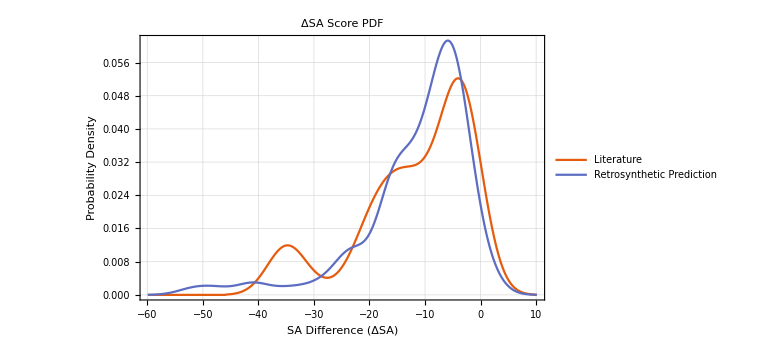
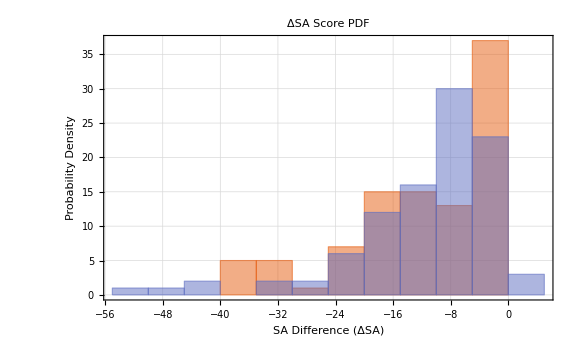
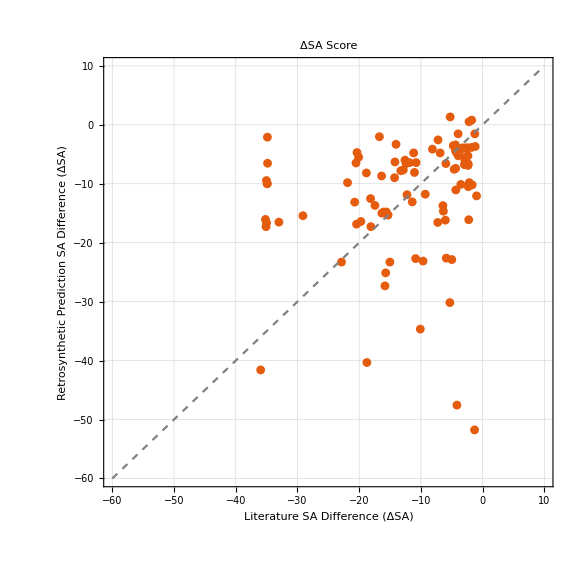
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Literature | -11.8725 | -9.47225 | 10.1077 | 102.166 | -35.9617 | -0.980856
Retrosynthetic Prediction | -11.5905 | -8.42494 | 9.95994 | 99.2003 | -51.7576 | 1.338,-Graphics-}

```mathematica
pltAndStat[tSADiff,retSADiff,"Literature","Retrosynthetic Prediction","SA",5]
```

```mathematica
(* What if we color the points by 'true' reaction class *)
```

```mathematica
trclass=DeleteDuplicates[Normal[allDatAnaly[[All,"true rclass"]]]]
```

{electrophilic aromatic substitution,amide formation,epoxide opening,conjugate addition,dielsalder,robinson,cyclisation,elimination,substitution,friedelcrafts,nucleophilic aromatic substitution,grignard,organocopper,acetylide,e-sub,amine}

```mathematica
rxnDatSA=Table[Thread[{allDatAnaly[[All,{"true rclass","true SA diff"}]][Select[#"true rclass"==trclass[[i]]&]],allDatAnaly[[All,{"true rclass","ret SA diff"}]][Select[#"true rclass"==trclass[[i]]&]]}],{i,1,Length@trclass}];
```

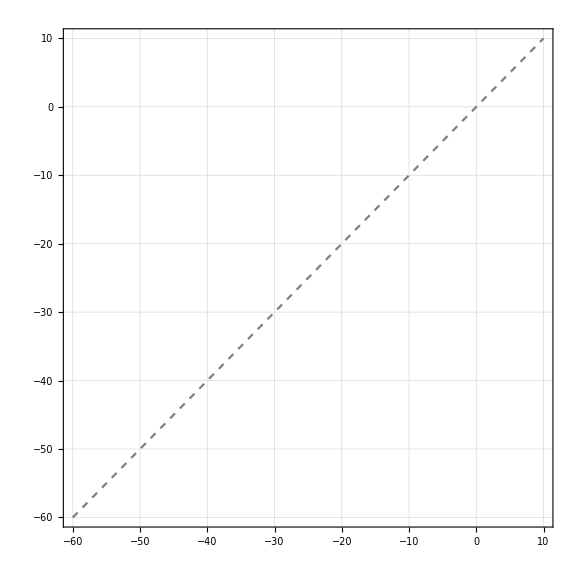

```mathematica
Show[ListPlot[Table[Transpose[Normal[#[[All,2]]]&/@rxnDatSA[[i]]],{i,1,Length@rxnDat}],PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,AspectRatio->1,PlotRange->{{-60,10},{-60,10}},PlotLegends->trclass],Plot[x,{x,-60,10},PlotStyle->{Gray,Dashed}]]
```

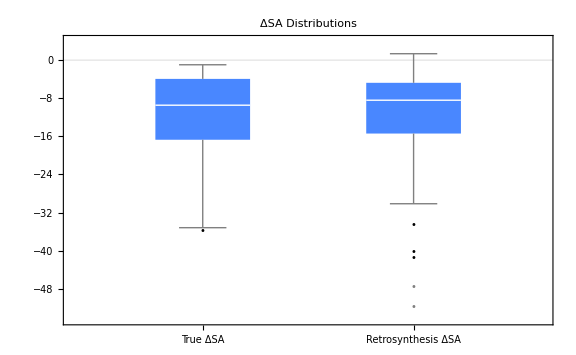

```mathematica
BoxWhiskerChart[{tSADiff,retSADiff},"Outliers",ChartLabels->{"True ΔSA","Retrosynthesis ΔSA"},PlotLabel->"ΔSA Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

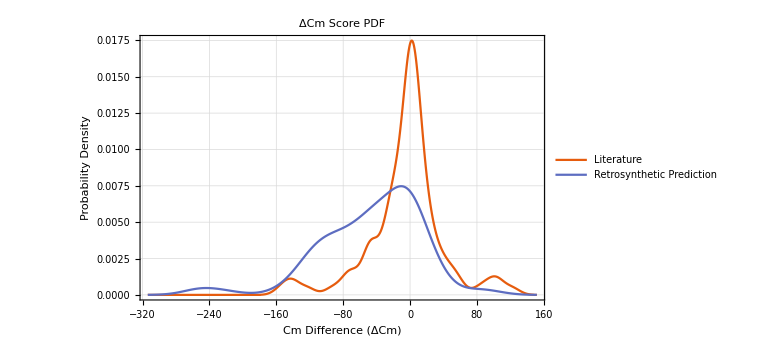
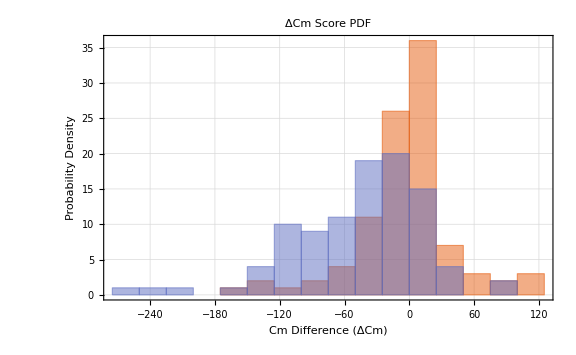
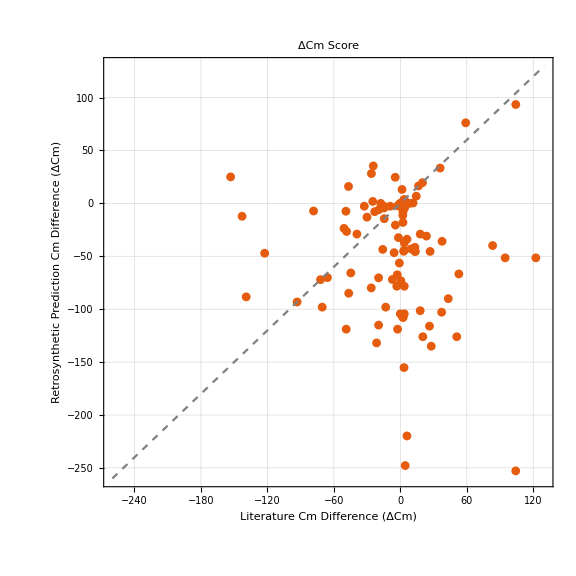
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Literature | -5.47219 | 1.02272 | 45.8289 | 2100.28 | -153.193 | 122.334
Retrosynthetic Prediction | -46.0117 | -38.5541 | 59.8801 | 3585.62 | -252.817 | 93.4612,-Graphics-}

```mathematica
pltAndStat[tCompDiff,retCompDiff,"Literature","Retrosynthetic Prediction","Cm",25]
```

```mathematica
rxnDatCM=Table[Thread[{allDatAnaly[[All,{"true rclass","true Cm diff"}]][Select[#"true rclass"==trclass[[i]]&]],allDatAnaly[[All,{"true rclass","ret Cm diff"}]][Select[#"true rclass"==trclass[[i]]&]]}],{i,1,Length@trclass}];
```

```mathematica
pltRange[tCompDiff,retCompDiff]
```

<|minR→-260,maxR→130|>

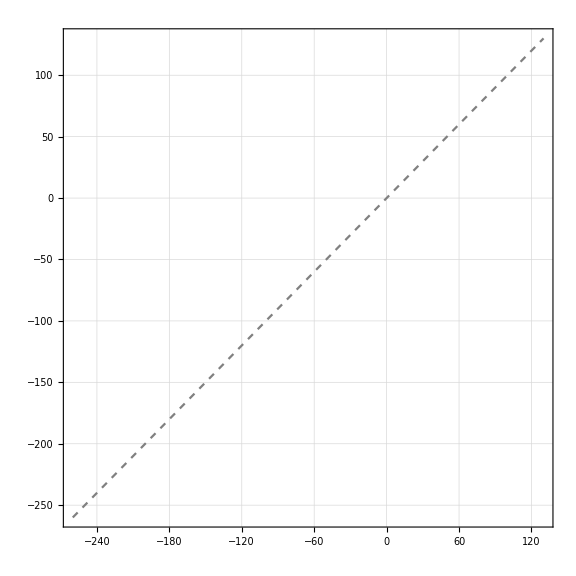

```mathematica
Show[ListPlot[Table[Transpose[Normal[#[[All,2]]]&/@rxnDatCM[[i]]],{i,1,Length@rxnDat}],PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,AspectRatio->1,PlotRange->{{-260,130},{-260,130}},PlotLegends->trclass],Plot[x,{x,-260,130},PlotStyle->{Gray,Dashed}]]
```

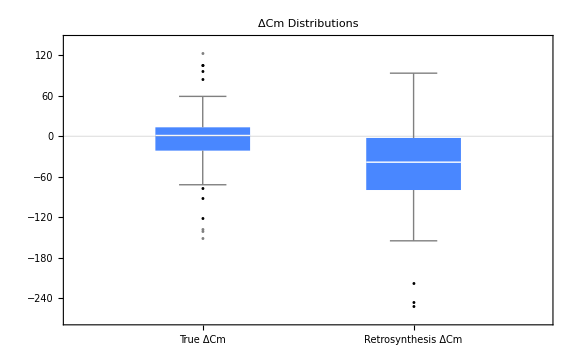

```mathematica
BoxWhiskerChart[{tCompDiff,retCompDiff},"Outliers",ChartLabels->{"True ΔCm","Retrosynthesis ΔCm"},PlotLabel->"ΔCm Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

```mathematica
SmoothHistogram[{tSADiff,retSADiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["SA Score PDF",Bold,Larger],FrameLabel->{"Synthetic Accessibility Score Difference (ΔSA)","Probability Density"},PlotLegends->{"Literature","Retrosynthetic Prediction"},ImageSize->Large,GridLines->Automatic];
```

```mathematica
{SmoothHistogram[{tCompDiff,retCompDiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["C_m Score PDF",Bold,Larger],FrameLabel->{"C_m Difference (ΔC_m)","Probability Density"},PlotLegends->{"Literature","Retrosynthetic Prediction"},ImageSize->Large,GridLines->Automatic],statTable[tCompDiff,retCompDiff,"Literature","Retrosynthetic Prediction"]};
```

#### Literature vs. Forward Prediction

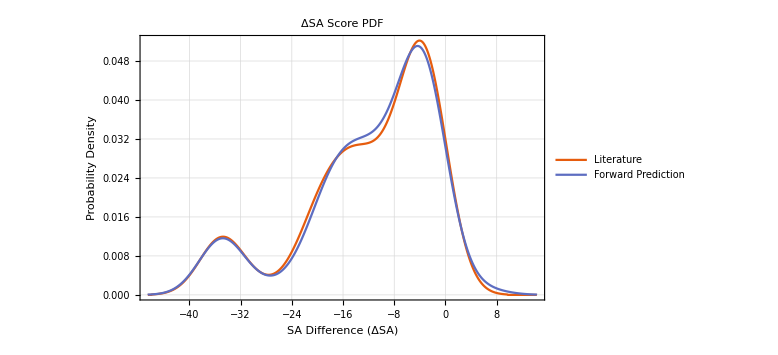
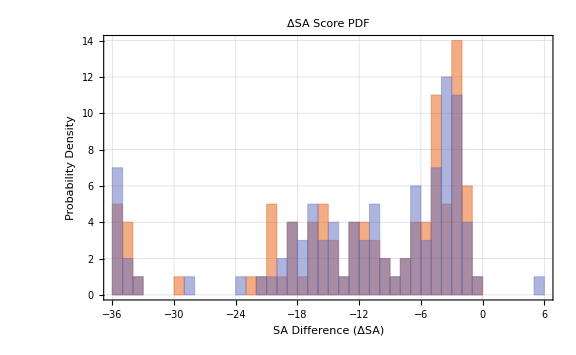
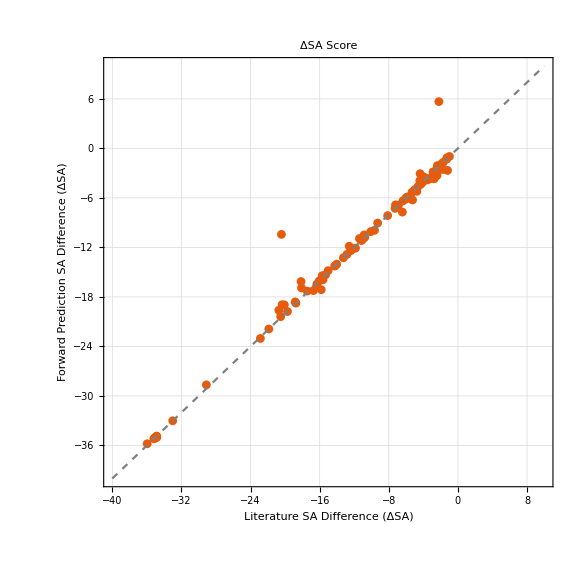
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Literature | -11.8725 | -9.47225 | 10.1077 | 102.166 | -35.9617 | -0.980856
Forward Prediction | -11.6825 | -9.48472 | 10.0894 | 101.796 | -35.7935 | 5.66694,-Graphics-}

```mathematica
pltAndStat[tSADiff,fRetSADiff,"Literature","Forward Prediction","SA",1]
```

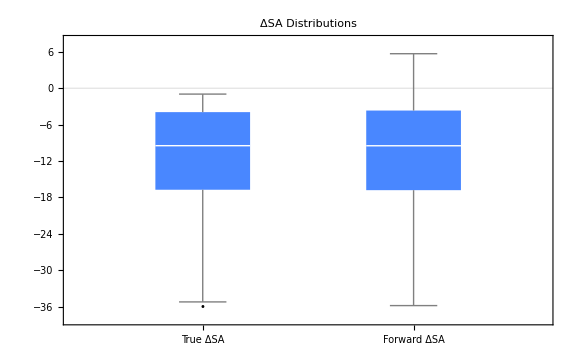

```mathematica
BoxWhiskerChart[{tSADiff,fRetSADiff},"Outliers",ChartLabels->{"True ΔSA","Forward ΔSA"},PlotLabel->"ΔSA Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

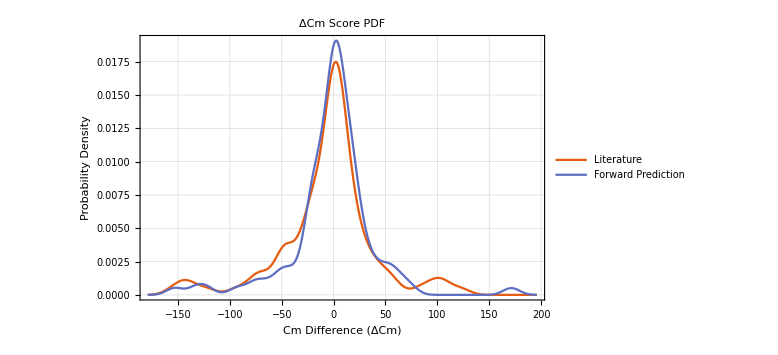
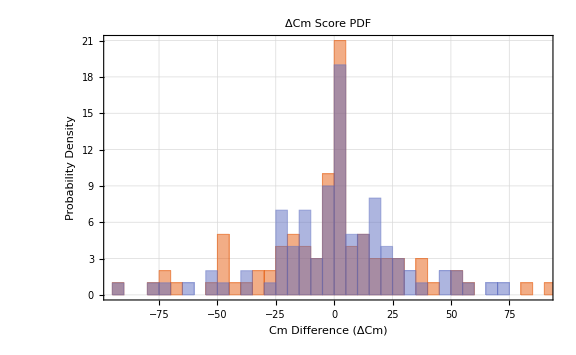
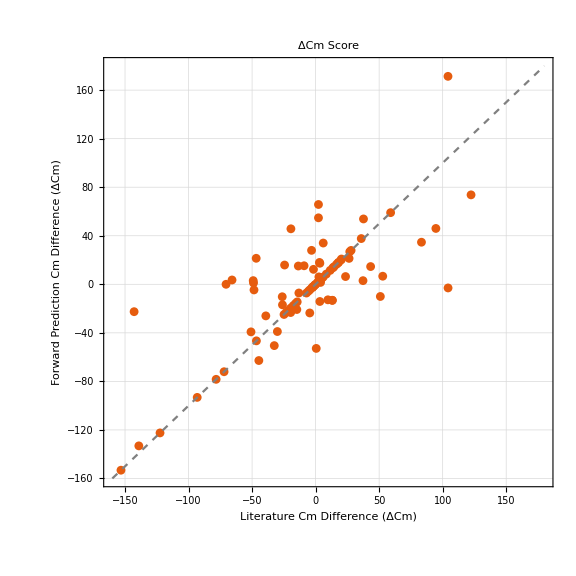
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Literature | -5.47219 | 1.02272 | 45.8289 | 2100.28 | -153.193 | 122.334
Forward Prediction | -2.05701 | 2.38529 | 40.773 | 1662.44 | -153.193 | 171.359,-Graphics-}

```mathematica
pltAndStat[tCompDiff,fRetCompDiff,"Literature","Forward Prediction","Cm",5]
```

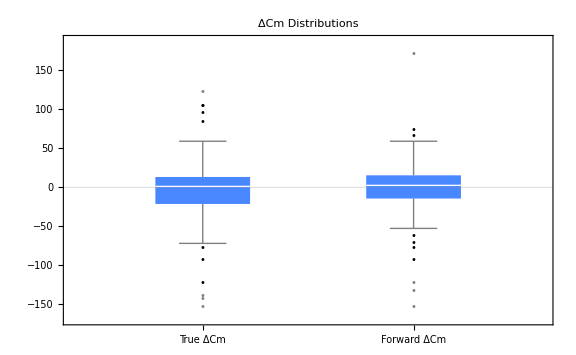

```mathematica
BoxWhiskerChart[{tCompDiff,fRetCompDiff},"Outliers",ChartLabels->{"True ΔCm","Forward ΔCm"},PlotLabel->"ΔCm Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

```mathematica
SmoothHistogram[{tSADiff,fRetSADiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["SA Score PDF",Bold,Larger],FrameLabel->{"Synthetic Accessibility Score Difference (ΔSA)","Probability Density"},PlotLegends->{"Literature","Forward Prediction"},ImageSize->Large,GridLines->Automatic];
```

```mathematica
{SmoothHistogram[{tCompDiff,fRetCompDiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["C_m Score PDF",Bold,Larger],FrameLabel->{"C_m Difference (ΔC_m)","Probability Density"},PlotLegends->{"Literature","Forward Prediction"},ImageSize->Large,GridLines->Automatic],statTable[tCompDiff,fRetCompDiff,"Literature","Forward Prediction"]};
```

#### Retrosynthetic Prediction vs. Canonical Retrosynthetic Prediction

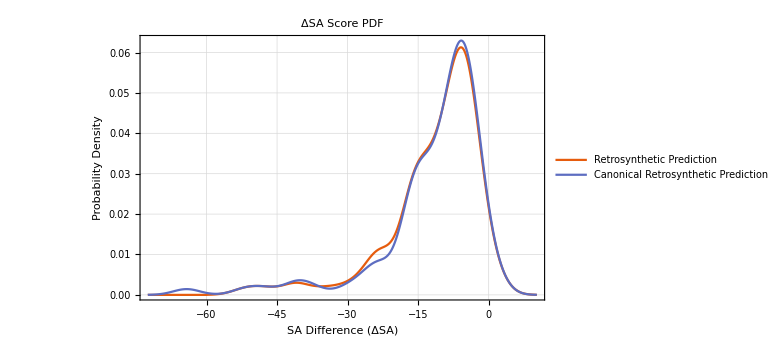
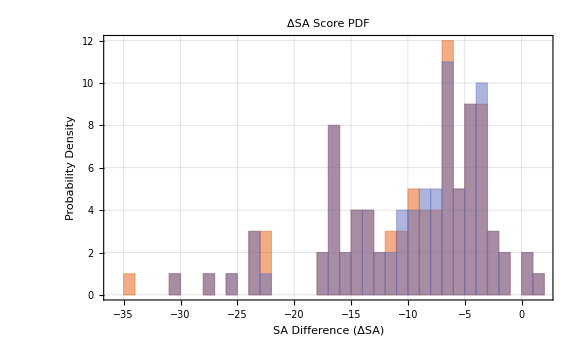
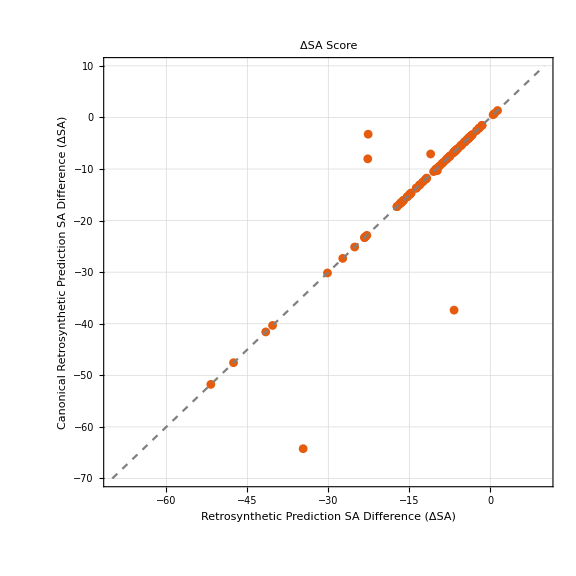
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Retrosynthetic Prediction | -11.5905 | -8.42494 | 9.95994 | 99.2003 | -51.7576 | 1.338
Canonical Retrosynthetic Prediction | -11.8223 | -8.05668 | 11.2844 | 127.337 | -64.2285 | 1.338,-Graphics-}

```mathematica
pltAndStat[retSADiff,cRetSADiff,"Retrosynthetic Prediction","Canonical Retrosynthetic Prediction","SA",1]
```

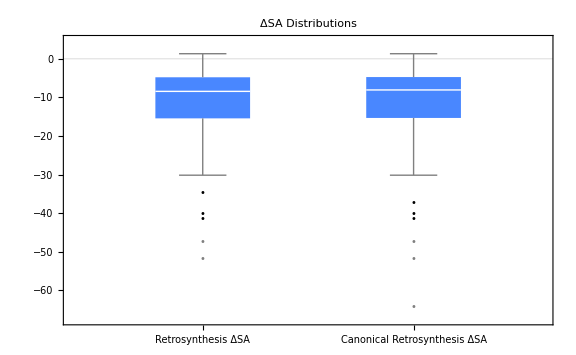

```mathematica
BoxWhiskerChart[{retSADiff,cRetSADiff},"Outliers",ChartLabels->{"Retrosynthesis ΔSA","Canonical Retrosynthesis ΔSA"},PlotLabel->"ΔSA Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

```mathematica
(* get outliers *)
```

```mathematica
lFitRetCret=LinearModelFit[Thread[{retSADiff,cRetSADiff}],x,x]
```

FittedModel[-0.0422224+1.01636 x]

```mathematica
lFitRetCret["FitResiduals"];
```

```mathematica
resDRetCret=Thread[{Abs[lFitRetCret["FitResiduals"]],Thread[{retSADiff,cRetSADiff}]}];(* {|residual|,{retSADiff,cRetSADiff}} *)
```

```mathematica
ReverseSortBy[resDRetCret,#[[1]]&];(* sorted by magnitude of residual *)
```

```mathematica
(* *)
```

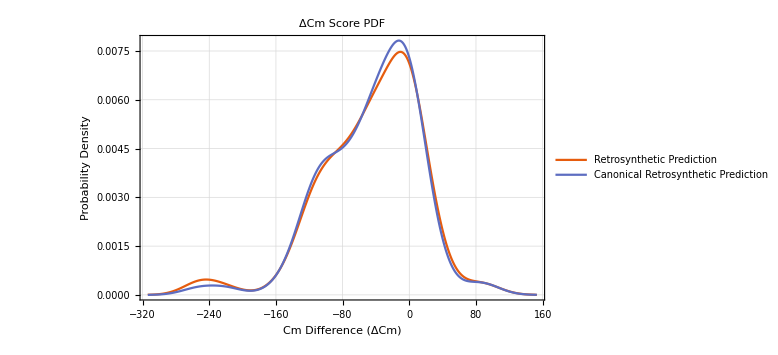
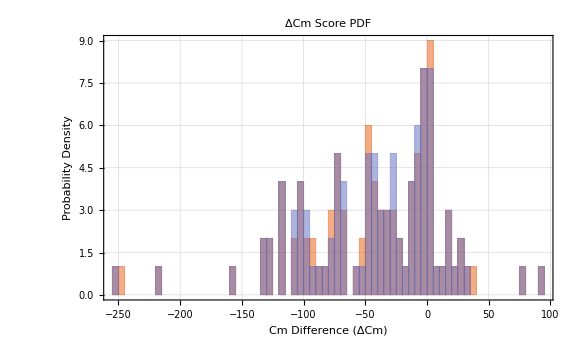
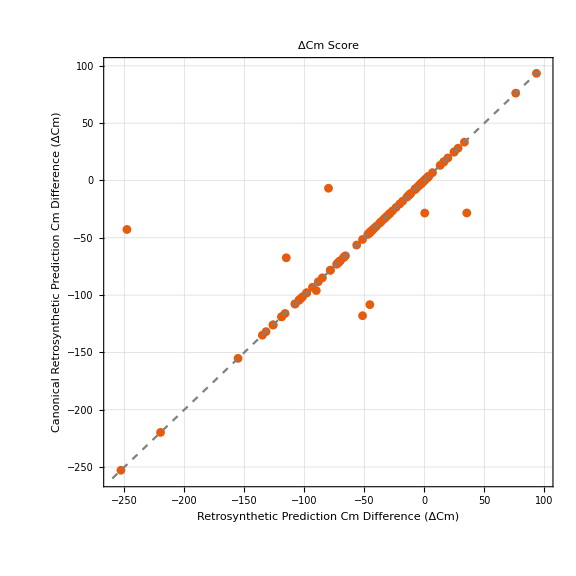
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Retrosynthetic Prediction | -46.0117 | -38.5541 | 59.8801 | 3585.62 | -252.817 | 93.4612
Canonical Retrosynthetic Prediction | -45.0147 | -36.5443 | 56.0303 | 3139.39 | -252.817 | 93.4612,-Graphics-}

```mathematica
pltAndStat[retCompDiff,cRetCompDiff,"Retrosynthetic Prediction","Canonical Retrosynthetic Prediction","Cm",5]
```

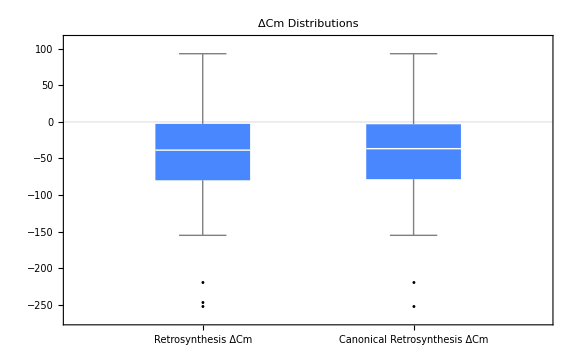

```mathematica
BoxWhiskerChart[{retCompDiff,cRetCompDiff},"Outliers",ChartLabels->{"Retrosynthesis ΔCm","Canonical Retrosynthesis ΔCm"},PlotLabel->"ΔCm Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

```mathematica
SmoothHistogram[{retSADiff,cRetSADiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["SA Score PDF",Bold,Larger],FrameLabel->{"Synthetic Accessibility Score Difference (ΔSA)","Probability Density"},PlotLegends->{"Retrosynthetic Prediction","Canonical Retrosynthetic Prediction"},ImageSize->Large,GridLines->Automatic];
```

```mathematica
{SmoothHistogram[{retCompDiff,cRetCompDiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["C_m Score PDF",Bold,Larger],FrameLabel->{"C_m Difference (ΔC_m)","Probability Density"},PlotLegends->{"Retrosynthetic Prediction","Canonical Retrosynthetic Prediction"},ImageSize->Large,GridLines->Automatic],statTable[retCompDiff,cRetCompDiff,"Retrosynthetic Prediction","Canonical Retrosynthetic Prediction"]};
```

#### Retrosynthetic Prediction vs. Forward Prediction

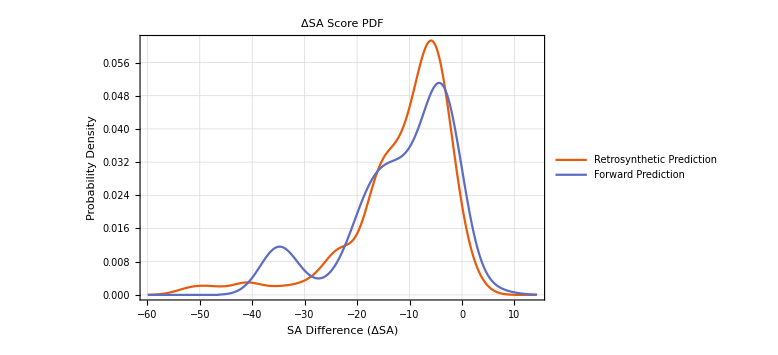
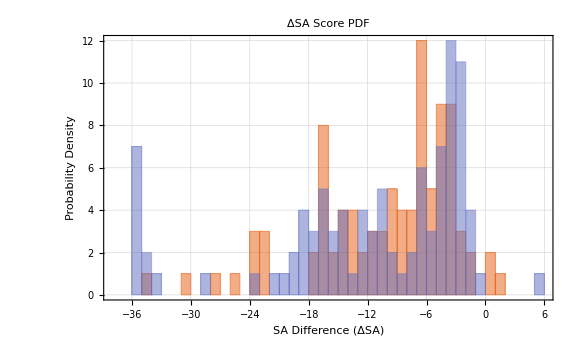
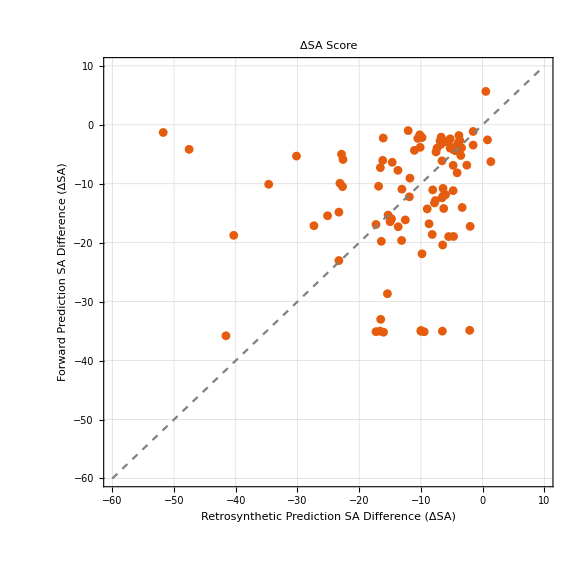
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Retrosynthetic Prediction | -11.5905 | -8.42494 | 9.95994 | 99.2003 | -51.7576 | 1.338
Forward Prediction | -11.6825 | -9.48472 | 10.0894 | 101.796 | -35.7935 | 5.66694,-Graphics-}

```mathematica
pltAndStat[retSADiff,fRetSADiff,"Retrosynthetic Prediction","Forward Prediction","SA",1]
```

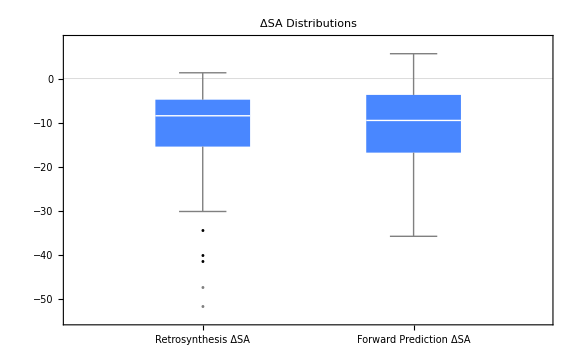

```mathematica
BoxWhiskerChart[{retSADiff,fRetSADiff},"Outliers",ChartLabels->{"Retrosynthesis ΔSA","Forward Prediction ΔSA"},PlotLabel->"ΔSA Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

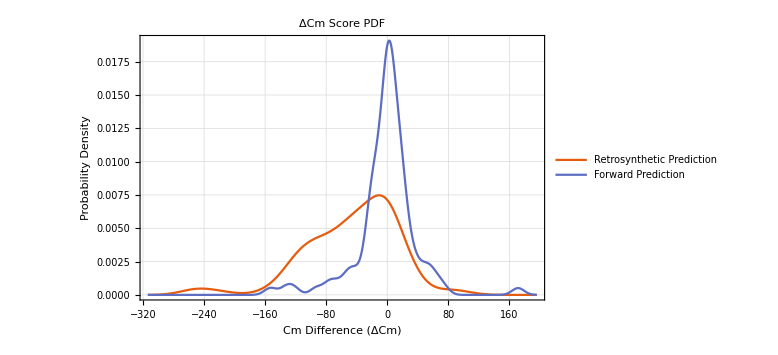
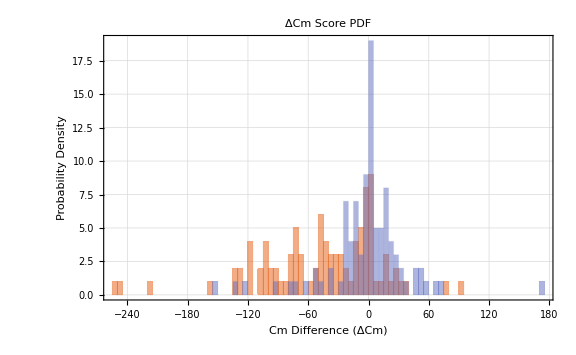
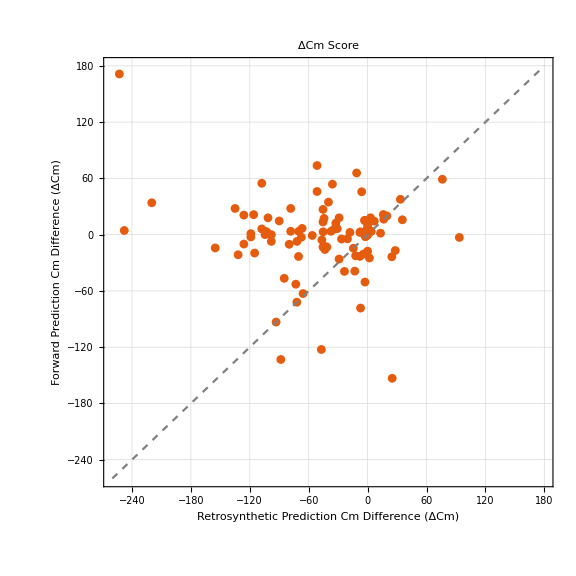
{-Graphics-,-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
Retrosynthetic Prediction | -46.0117 | -38.5541 | 59.8801 | 3585.62 | -252.817 | 93.4612
Forward Prediction | -2.05701 | 2.38529 | 40.773 | 1662.44 | -153.193 | 171.359,-Graphics-}

```mathematica
pltAndStat[retCompDiff,fRetCompDiff,"Retrosynthetic Prediction","Forward Prediction","Cm",5]
```

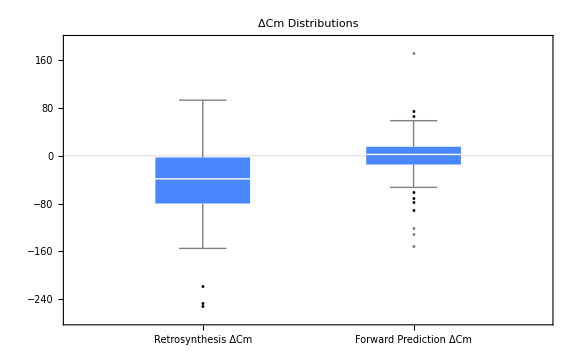

```mathematica
BoxWhiskerChart[{retCompDiff,fRetCompDiff},"Outliers",ChartLabels->{"Retrosynthesis ΔCm","Forward Prediction ΔCm"},PlotLabel->"ΔCm Distributions",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

```mathematica
SmoothHistogram[{retSADiff,fRetSADiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["SA Score PDF",Bold,Larger],FrameLabel->{"Synthetic Accessibility Score Difference (ΔSA)","Probability Density"},PlotLegends->{"Retrosynthetic Prediction","Forward Prediction"},ImageSize->Large,GridLines->Automatic];
```

```mathematica
{SmoothHistogram[{retCompDiff,fRetCompDiff},Automatic,"PDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["C_m Score PDF",Bold,Larger],FrameLabel->{"C_m Difference (ΔC_m)","Probability Density"},PlotLegends->{"Retrosynthetic Prediction","Forward Prediction"},ImageSize->Large,GridLines->Automatic],statTable[retCompDiff,fRetCompDiff,"Retrosynthetic Prediction","Forward Prediction"]};
```

#### Literature vs. Retrosynthetic Prediction - CDF

```mathematica
SmoothHistogram[{tSADiff,retSADiff},Automatic,"CDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["SA Score CDF",Bold,Larger],FrameLabel->{"Synthetic Accessibility Score Difference (ΔSA)","Probability Density"},PlotLegends->{"Literature","Retrosynthetic Prediction"},ImageSize->Large,GridLines->Automatic];
```

```mathematica
{SmoothHistogram[{tCompDiff,retCompDiff},Automatic,"CDF",PlotTheme->{"Scientific","Temperature"},PlotLabel->Style["C_m Score CDF",Bold,Larger],FrameLabel->{"C_m Difference (ΔC_m)","Probability Density"},PlotLegends->{"Literature","Retrosynthetic Prediction"},ImageSize->Large,GridLines->Automatic],statTable[tCompDiff,retCompDiff,"Literature","Retrosynthetic Prediction"]};
```

### Bisectrix Venn-Diagram Scatter Plots

#### Literature vs. Retrosynthetic Prediction

```mathematica
(* we want to keep the points that are above both bisectrixes *)
```

```mathematica
{sctPlt[tSADiff,retSADiff,"Literature","Retrosynthetic Prediction","SA"],sctPlt[tCompDiff,retCompDiff,"Literature","Retrosynthetic Prediction","Cm"]}
```

{-Graphics-,-Graphics-}

```mathematica
aSAbisTR=allDatAnaly[Select[#"ret SA diff">#"true SA diff"&]];
```

```mathematica
aCMbisTR=allDatAnaly[Select[#"ret Cm diff">#"true Cm diff"&]];
```

```mathematica
abvTRBis=Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true rsmiles"==i&]],{i,Intersection[Normal@aSAbisTR[[All,"true rsmiles"]],Normal@aCMbisTR[[All,"true rsmiles"]]]}]]]];
```

```mathematica
(* What about both below? *)
```

```mathematica
bSAbisTR=allDatAnaly[Select[#"ret SA diff"<#"true SA diff"&]];
```

```mathematica
bCMbisTR=allDatAnaly[Select[#"ret Cm diff"<#"true Cm diff"&]];
```

```mathematica
blwTRBis=Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true rsmiles"==i&]],{i,Intersection[Normal@bSAbisTR[[All,"true rsmiles"]],Normal@bCMbisTR[[All,"true rsmiles"]]]}]]]];
```

```mathematica
(* check to make sure it was done right *)
```

```mathematica
{sctPlt[Normal[#[[All,"true SA diff"]]],Normal[#[[All,"ret SA diff"]]],"Lit SA","Ret SA","SA"],sctPlt[Normal[#[[All,"true Cm diff"]]],Normal[#[[All,"ret Cm diff"]]],"Lit Cm","Ret Cm","Cm"]}&@abvTRBis;
```

```mathematica
{sctPlt[Normal[#[[All,"true SA diff"]]],Normal[#[[All,"ret SA diff"]]],"Lit SA","Ret SA","SA"],sctPlt[Normal[#[[All,"true Cm diff"]]],Normal[#[[All,"ret Cm diff"]]],"Lit Cm","Ret Cm","Cm"]}&@blwTRBis;
```

```mathematica
(* plot the dists *)
```

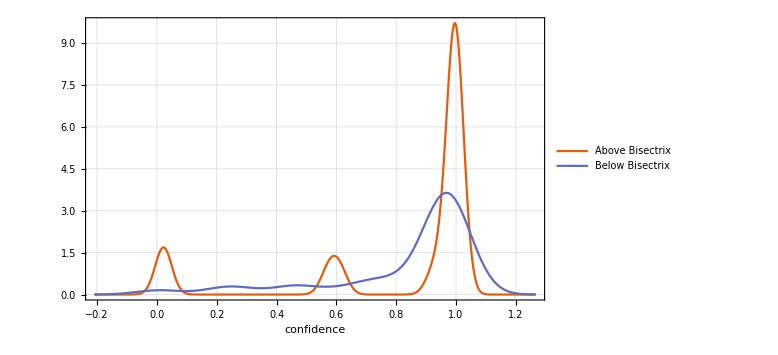
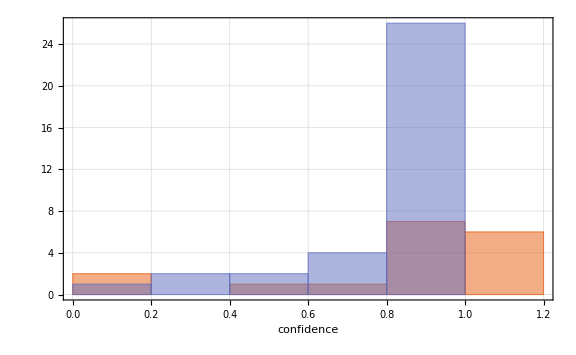

```mathematica
{SmoothHistogram[{Normal@abvTRBis[[All,"ret confidence"]],Normal@blwTRBis[[All,"ret confidence"]]},PlotTheme->"Scientific",GridLines->Automatic,PlotLegends->{"Above Bisectrix","Below Bisectrix"},PlotRange->Full,ImageSize->Large,FrameLabel->{"confidence",""}],Histogram[{Normal@abvTRBis[[All,"ret confidence"]],Normal@blwTRBis[[All,"ret confidence"]]},{0.2},PlotTheme->"Scientific",GridLines->Automatic,PlotRange->Full,ImageSize->Large,FrameLabel->{"confidence",""}]}
```

#### Literature vs. Forward Prediction

```mathematica
(* we want to keep the points that are above both bisectrixes *)
```

```mathematica
{sctPlt[tSADiff,fRetSADiff,"Literature","Retrosynthetic Prediction","SA"],sctPlt[tCompDiff,fRetCompDiff,"Literature","Retrosynthetic Prediction","Cm"]};
```

```mathematica
aSAbisTFr=allDatAnaly[Select[#"forward pred SA diff">#"true SA diff"&]];
```

```mathematica
aCMbisTFr=allDatAnaly[Select[#"forward pred SA diff">#"true Cm diff"&]];
```

```mathematica
abvTFrBis=Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true rsmiles"==i&]],{i,Intersection[Normal@aSAbisTFr[[All,"true rsmiles"]],Normal@aCMbisTFr[[All,"true rsmiles"]]]}]]]];
```

```mathematica
(* What about both below? *)
```

```mathematica
bSAbisTFr=allDatAnaly[Select[#"forward pred SA diff"<#"true SA diff"&]];
```

```mathematica
bCMbisTFr=allDatAnaly[Select[#"forward pred Cm diff"<#"true Cm diff"&]];
```

```mathematica
blwTFrBis=Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true rsmiles"==i&]],{i,Intersection[Normal@bSAbisTFr[[All,"true rsmiles"]],Normal@bCMbisTFr[[All,"true rsmiles"]]]}]]]];
```

```mathematica
(* check to make sure it was done right *)
```

```mathematica
{sctPlt[Normal[#[[All,"true SA diff"]]],Normal[#[[All,"forward pred SA diff"]]],"Lit SA","Fwd Ret SA","SA"],sctPlt[Normal[#[[All,"true Cm diff"]]],Normal[#[[All,"ret Cm diff"]]],"Lit Cm","Fwd Ret Cm","Cm"]}&@abvTFrBis;
```

```mathematica
{sctPlt[Normal[#[[All,"true SA diff"]]],Normal[#[[All,"forward pred SA diff"]]],"Lit SA","Fwd Ret SA","SA"],sctPlt[Normal[#[[All,"true Cm diff"]]],Normal[#[[All,"forward pred Cm diff"]]],"Lit Cm","Fwd Ret Cm","Cm"]}&@blwTFrBis;
```

```mathematica
(* plot the dists *)
```

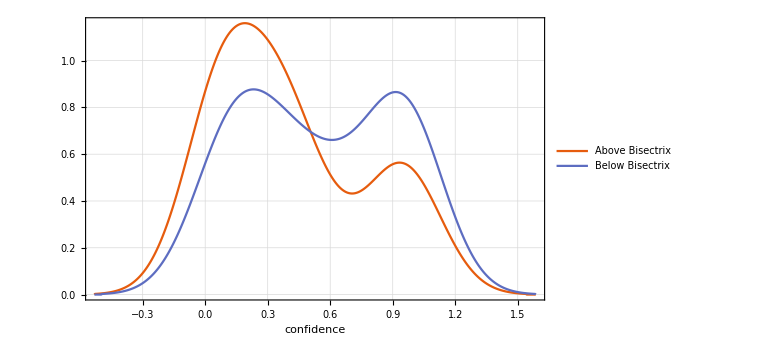
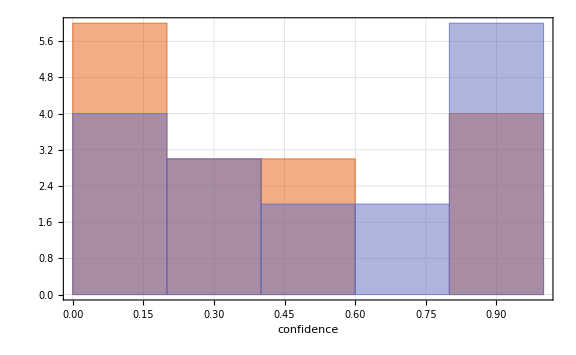

```mathematica
{SmoothHistogram[{Normal@abvTFrBis[[All,"forward pred confidence"]],Normal@blwTFrBis[[All,"forward pred confidence"]]},PlotTheme->"Scientific",GridLines->Automatic,PlotLegends->{"Above Bisectrix","Below Bisectrix"},PlotRange->Full,ImageSize->Large,FrameLabel->{"confidence",""}],Histogram[{Normal@abvTFrBis[[All,"forward pred confidence"]],Normal@blwTFrBis[[All,"forward pred confidence"]]},{0.2},PlotTheme->"Scientific",GridLines->Automatic,PlotRange->Full,ImageSize->Large,FrameLabel->{"confidence",""}]}
```

### Confidence Distributions

#### Literature vs. Retrosynthetic Prediction

```mathematica
allDatAnaly//First//Keys//Normal
```

{reaction number,true rclass,true rsmiles,true reacs,true prod,notes,true SA diff,true Cm diff,canonical true rsmiles,canonical true reacs,canonical true prod,canonical true SA diff,canonical true Cm diff,project ID,ret ID,ret pred rclass,ret pred rsmiles,ret pred reacs,ret confidence,ret optimization,ret SA diff,ret Cm diff,canonical ret ID,canonical ret pred rsmiles,canonical ret pred reacs,canonical ret confidence,canonical ret optimization,canonical ret SA diff,canonical ret Cm diff,forward pred ID,forward pred rsmiles,forward pred reacs,forward pred prod,forward pred confidence,forward pred SA diff,forward pred Cm diff,ret and canonical pred sameQ,ret and forward pred sameQ}

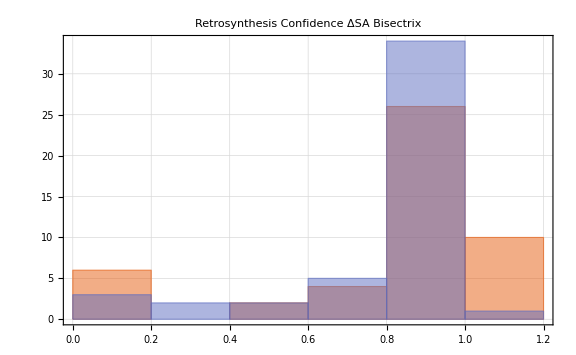
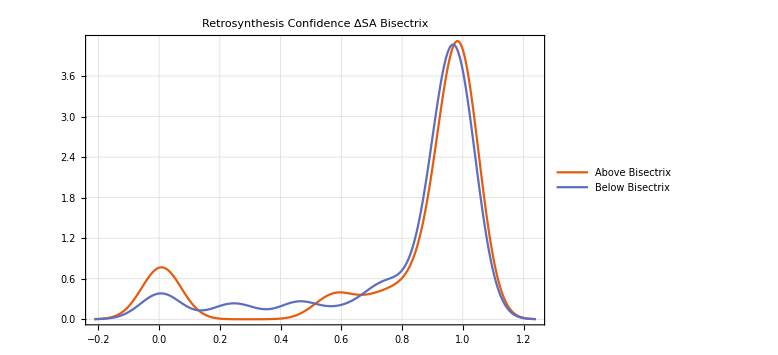

```mathematica
{Histogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,retSADiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"ret confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,retSADiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"ret confidence"]]]},{0.2},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotLabel->"Retrosynthesis Confidence\n ΔSA Bisectrix"],SmoothHistogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,retSADiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"ret confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,retSADiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"ret confidence"]]]},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotRange->All,PlotLegends->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Retrosynthesis Confidence\n ΔSA Bisectrix"]}
```

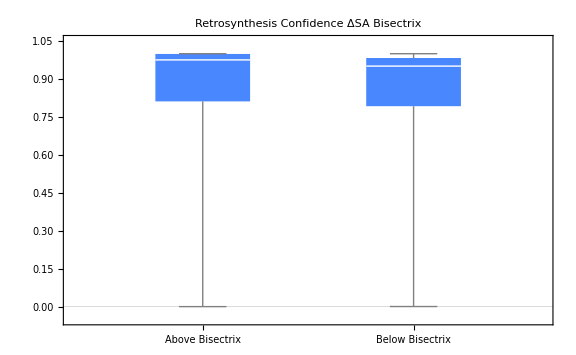

```mathematica
BoxWhiskerChart[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,retSADiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"ret confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,retSADiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"ret confidence"]]]},ChartLabels->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Retrosynthesis Confidence\n ΔSA Bisectrix",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

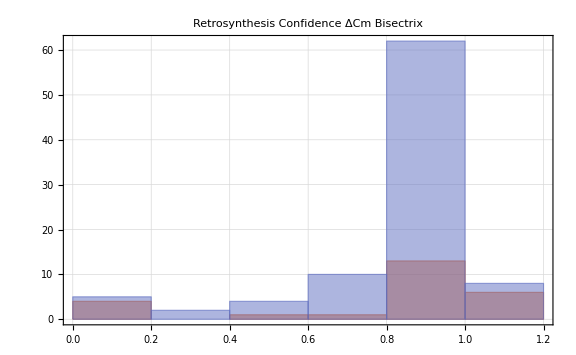
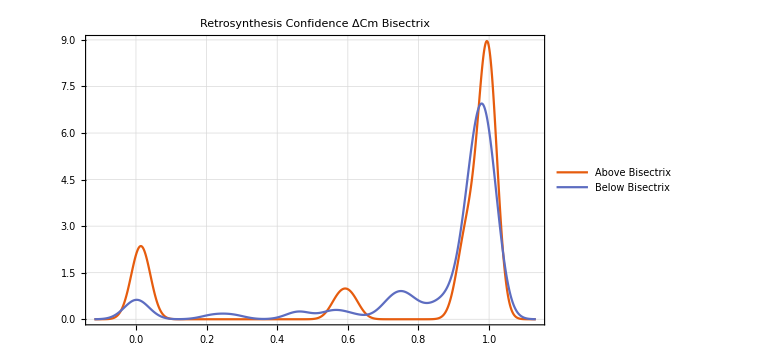

```mathematica
{Histogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,retCompDiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"ret confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,retCompDiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"ret confidence"]]]},{0.2},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotLabel->"Retrosynthesis Confidence\n ΔCm Bisectrix"],SmoothHistogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,retCompDiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"ret confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,retCompDiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"ret confidence"]]]},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotRange->All,PlotLegends->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Retrosynthesis Confidence\n ΔCm Bisectrix"]}
```

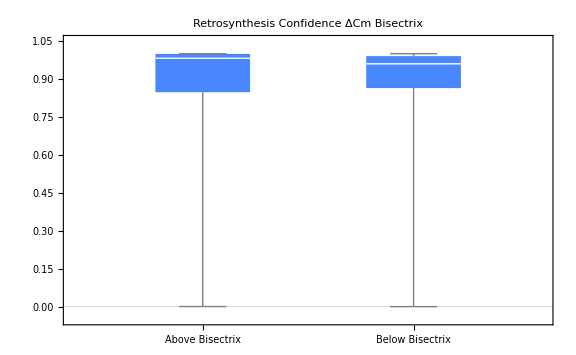

```mathematica
BoxWhiskerChart[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,retCompDiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"ret confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,retCompDiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"ret confidence"]]]},ChartLabels->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Retrosynthesis Confidence\n ΔCm Bisectrix",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

#### Literature vs. Forward Prediction

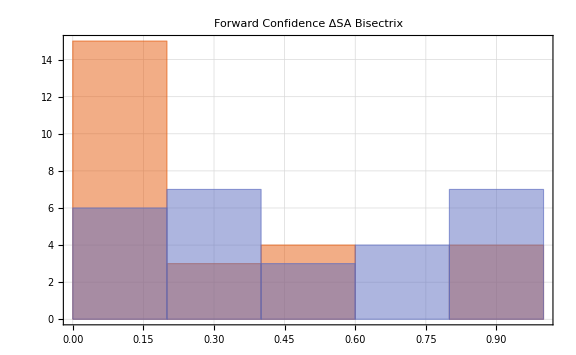
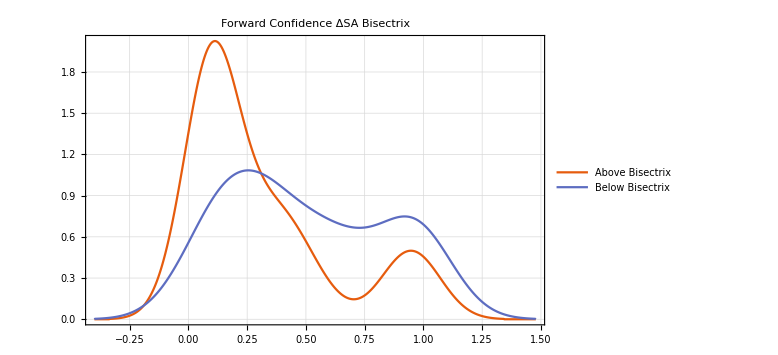

```mathematica
{Histogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,fRetSADiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"forward pred confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,fRetSADiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"forward pred confidence"]]]},{0.2},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotLabel->"Forward Confidence\nΔSA Bisectrix"],SmoothHistogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,fRetSADiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"forward pred confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,fRetSADiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"forward pred confidence"]]]},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotRange->All,PlotLegends->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Forward Confidence\nΔSA Bisectrix"]}
```

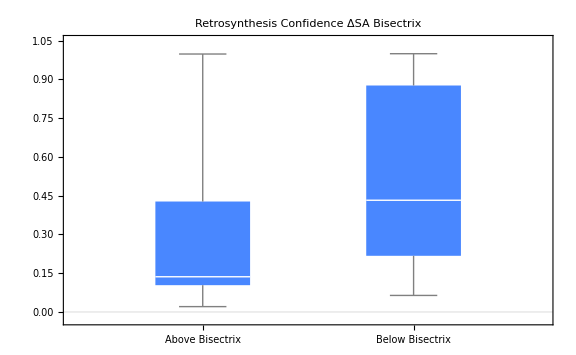

```mathematica
BoxWhiskerChart[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,fRetSADiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"forward pred confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true SA diff"==i&]],{i,Select[Thread[{tSADiff,fRetSADiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"forward pred confidence"]]]},ChartLabels->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Retrosynthesis Confidence\n ΔSA Bisectrix",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

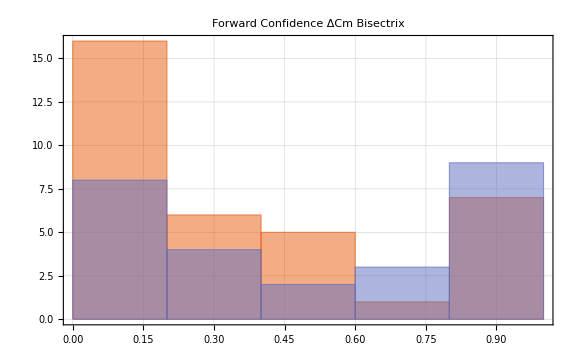
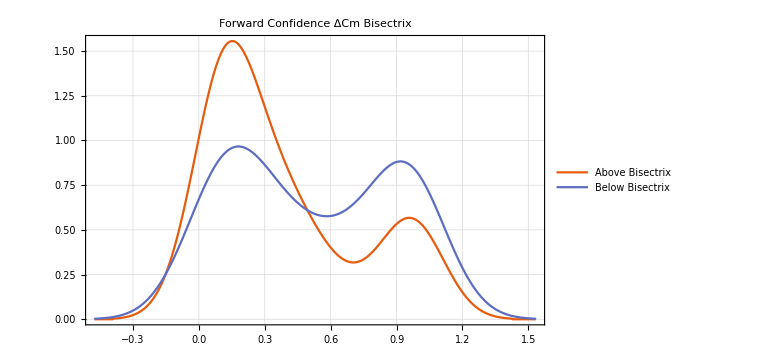

```mathematica
{Histogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,fRetCompDiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"forward pred confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,fRetCompDiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"forward pred confidence"]]]},{0.2},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotLabel->"Forward Confidence\nΔCm Bisectrix"],SmoothHistogram[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,fRetCompDiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"forward pred confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,fRetCompDiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"forward pred confidence"]]]},PlotTheme->{"Scientific","Temperature"},ImageSize->Large,GridLines->Automatic,PlotRange->All,PlotLegends->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Forward Confidence\nΔCm Bisectrix"]}
```

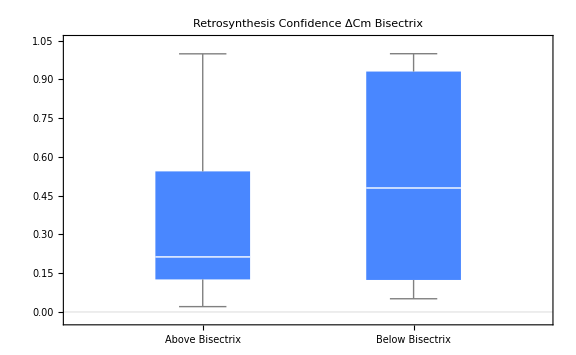

```mathematica
BoxWhiskerChart[{Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,fRetCompDiff}],#[[2]]>#[[1]]&][[All,1]]}]]]][[All,"forward pred confidence"]]],Normal[Dataset[Flatten[Normal[Table[allDatAnaly[Select[#"true Cm diff"==i&]],{i,Select[Thread[{tCompDiff,fRetCompDiff}],#[[1]]>#[[2]]&][[All,1]]}]]]][[All,"forward pred confidence"]]]},ChartLabels->{"Above Bisectrix","Below Bisectrix"},PlotLabel->"Retrosynthesis Confidence\n ΔCm Bisectrix",PlotTheme->{"Scientific","CoolColor"},ImageSize->Large]
```

## Sameness of Retrosynthetic and Canonical Retrosynthetic Predictions

```mathematica
rxnPlt[rsmiles_String,title_String,rclass_String]:=Module[{plus=Graphics[Text@Style["+",20],BaselinePosition->Center,ImageSize->100],arrow=Graphics[Text@Style["→",20],BaselinePosition->Center,ImageSize->100],reacsplit,reacs,prods,reacPlots,prodPlots},
reacsplit=reacSplit[rsmiles];
reacs=StringSplit[reacsplit[[1]],"."];
prods=StringSplit[reacsplit[[2]],"."];
reacPlots=Table[MoleculePlot[Molecule[i],ImageSize->Large],{i,reacs}];
prodPlots=Table[MoleculePlot[Molecule[j],ImageSize->Large],{j,prods}];
Show[GraphicsRow[Flatten[{Riffle[reacPlots,plus],arrow,Riffle[prodPlots,plus]}],ImageSize->Full,Frame->True],PlotLabel->title<>"\n"<>rclass,LabelStyle->{FontFamily->"Cambria",12,GrayLevel[0]}]
]
```

```mathematica
(* Counts of reactions where the ret and canonical ret preds are same or not same *)
```

```mathematica
falseCanRet=Position[Normal[allDatAnaly[[All,"ret and canonical pred sameQ"]]],False];
```

```mathematica
{Counts@Normal[allDatAnaly[[All,"ret and canonical pred sameQ"]]],falseCanRet}
```

{<|True→91,False→7|>,{{3},{20},{23},{29},{75},{79},{95}}}

```mathematica
(* let's take the top 10 |residual| from the Subscript[ΔSA, ret] vs. Subscript[ΔSA, cret] data linear fit as candidates for these reactions *)
```

```mathematica
Take[ReverseSortBy[resDRetCret,#[[1]]&],10]
```

{{30.4942,{-6.71548,-37.3618}},{28.9581,{-34.661,-64.2285}},{19.7843,{-22.6235,-3.25164}},{15.0769,{-22.693,-8.0297}},{4.18778,{-11.0518,-7.08707}},{0.889058,{-51.7576,-51.7576}},{0.820295,{-47.5548,-47.5548}},{0.722684,{-41.589,-41.589}},{0.702053,{-40.3281,-40.3281}},{0.535654,{-30.1579,-30.1579}}}

```mathematica
(* the first 5 seem to be striking visual outliers from the y=x line *)
```

```mathematica
ReverseSortBy[resDRetCret,#[[1]]&][[1;;5]][[All,2]](* sorted by magnitude of residual *)
```

{{-6.71548,-37.3618},{-34.661,-64.2285},{-22.6235,-3.25164},{-22.693,-8.0297},{-11.0518,-7.08707}}

```mathematica
Position[Thread[{Normal@allDatAnaly[[All,"ret SA diff"]],Normal@allDatAnaly[[All,"canonical ret SA diff"]]}],#]&/@ReverseSortBy[resDRetCret,#[[1]]&][[1;;5]][[All,2]]
```

{{{23}},{{95}},{{29}},{{75}},{{3}}}

#### Reaction #3

SMs: match
Product: match (stereochemistry)
RClass: match
ΔConf: 0.009
ΔOpt: 0.19

```mathematica
falseCanRet[[1]]
```

{3}

```mathematica
rxn3=First[allDatAnaly[[falseCanRet[[1]]]]];
```

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn3]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn3]
```

0.009

-0.19

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn3
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -4.33634 | -11.0518 | -7.08707 | -4.33634
Conf | - | 0.946 | 0.937 | 0.70255
Opt | - | 1.04 | 1.23 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{#["ret SA diff"],#["canonical ret SA diff"]}]&@rxn3
```

True

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn3
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn3
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn3
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #20

SMs: match
Product: match (stereochemistry)
RClass: match
ΔConf: 0.301
ΔOpt: 0.368

```mathematica
falseCanRet[[2]]
```

{20}

```mathematica
rxn19=First[allDatAnaly[[falseCanRet[[2]]]]];
```

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn19]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn19]
```

-0.301

-0.368

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn19
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -4.36401 | -7.3926 | -7.3926 | -3.96315
Conf | - | 0.469 | 0.77 | 0.335765
Opt | - | 0.432 | 0.8 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{rxn19["ret SA diff"],rxn19["canonical ret SA diff"]}]
```

False

```mathematica
rxnPlt[rxn19["true rsmiles"],"True Reaction",rxn19["true rclass"]]
rxnPlt[rxn19["ret pred rsmiles"],"Retrosynthetic Prediction",rxn19["ret pred rclass"]]
rxnPlt[rxn19["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn19["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #23

SMs: different
Product: match
RClass: different
ΔConf: 0.01508
ΔOpt: 0.01641

```mathematica
falseCanRet[[3]]
```

{23}

```mathematica
rxn22=First[allDatAnaly[[falseCanRet[[3]]]]];
```

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn22]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn22]
```

-0.01508

-0.01641

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn22
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.37895 | -6.71548 | -37.3618 | -2.09308
Conf | - | 0.00992 | 0.025 | 0.40316
Opt | - | 0.00849 | 0.0249 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{rxn22["ret SA diff"],rxn22["canonical ret SA diff"]}]
```

True

```mathematica
rxnPlt[rxn22["true rsmiles"],"True Reaction",rxn22["true rclass"]]
rxnPlt[rxn22["ret pred rsmiles"],"Retrosynthetic Prediction",rxn22["ret pred rclass"]]
rxnPlt[rxn22["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn22["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #29

SMs: different
Product: same (stereochemistry)
RClass: different
ΔConf: 0.015
ΔOpt: 0.238

```mathematica
falseCanRet[[4]]
```

{29}

```mathematica
rxn29=First[allDatAnaly[[falseCanRet[[4]]]]];
```

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn29]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn29]
```

-0.015

0.238

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn29
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -5.88521 | -22.6235 | -3.25164 | -5.88521
Conf | - | 0.983 | 0.998 | 0.924006
Opt | - | 1.04 | 0.802 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{rxn28["ret SA diff"],rxn28["canonical ret SA diff"]}]
```

False

```mathematica
rxnPlt[rxn28["true rsmiles"],"True Reaction",rxn28["true rclass"]]
rxnPlt[rxn28["ret pred rsmiles"],"Retrosynthetic Prediction",rxn28["ret pred rclass"]]
rxnPlt[rxn28["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn28["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

rxnPlt[rxn28[true rsmiles],True Reaction,rxn28[true rclass]]

rxnPlt[rxn28[ret pred rsmiles],Retrosynthetic Prediction,rxn28[ret pred rclass]]

ReverseSortBy::normal: Nonatomic expression expected at position 1 in ReverseSortBy[#conf&][rclass].

rxnPlt[rxn28[canonical ret pred rsmiles],Canonical Retrosynthetic Prediction,ReverseSortBy[#conf&][rclass]]

#### Reaction #75

SMs: different
Product: same (stereochemistry)
RClass: different
ΔConf: 0.132
ΔOpt: 0.288

```mathematica
falseCanRet[[5]]
```

{75}

```mathematica
rxn75=First[allDatAnaly[[falseCanRet[[5]]]]];
```

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn75]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn75]
```

-0.132

-0.288

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn75
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -10.8536 | -22.693 | -8.0297 | -10.4877
Conf | - | 0.863 | 0.995 | 0.0634049
Opt | - | 0.892 | 1.18 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{rxn74["ret SA diff"],rxn74["canonical ret SA diff"]}]
```

False

```mathematica
rxnPlt[rxn75["true rsmiles"],"True Reaction",rxn75["true rclass"]]
rxnPlt[rxn75["ret pred rsmiles"],"Retrosynthetic Prediction",rxn75["ret pred rclass"]]
rxnPlt[rxn75["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn75["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #79

SMs: different
Product: same
RClass: different
ΔConf: 0.039
ΔOpt: 0.014

```mathematica
falseCanRet[[6]]
```

{79}

```mathematica
MoleculePlot@Molecule@reacSplit[rxn78["ret pred rsmiles"]][[2]];
MoleculePlot@Molecule@reacSplit[rxn78["canonical ret pred rsmiles"]][[2]];
```

```mathematica
rxn78=First[allDatAnaly[[falseCanRet[[6]]]]];
```

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn78]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn78]
```

-0.039

0.014

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn78
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -21.8876 | -9.81443 | -10.323 | -21.8876
Conf | - | 0.901 | 0.94 | 0.911891
Opt | - | 0.892 | 0.878 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{rxn78["ret SA diff"],rxn78["canonical ret SA diff"]}]
```

False

```mathematica
(* what rank is it? *)
```

```mathematica
Position[ReverseSortBy[resDRetCret,#[[1]]&][[All,2]],{rxn78["ret SA diff"],rxn78["canonical ret SA diff"]}]
```

{{25}}

```mathematica
rxnPlt[rxn78["true rsmiles"],"True Reaction",rxn78["true rclass"]]
rxnPlt[rxn78["ret pred rsmiles"],"Retrosynthetic Prediction",rxn78["ret pred rclass"]]
rxnPlt[rxn78["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn78["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #95

SMs: possibly same
Product: same
RClass: both unrecognized, possible same
ΔConf: 0.334
ΔOpt: 0.372

```mathematica
Normal[#["ret confidence"]-#["canonical ret confidence"]&@rxn94]
Normal[#["ret optimization"]-#["canonical ret optimization"]&@rxn94]
```

0.334

0.372

```mathematica
falseCanRet[[7]]
```

{95}

```mathematica
rxn94=First[allDatAnaly[[falseCanRet[[7]]]]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn94
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -10.0931 | -34.661 | -64.2285 | -10.0931
Conf | - | 0.612 | 0.278 | 0.243712
Opt | - | 0.693 | 0.321 | -

```mathematica
(* is it a top 5 residual? *)
```

```mathematica
MemberQ[Take[ReverseSortBy[resDRetCret,#[[1]]&],5][[All,2]],{rxn94["ret SA diff"],rxn94["canonical ret SA diff"]}]
```

True

-Graphics-

-Graphics-

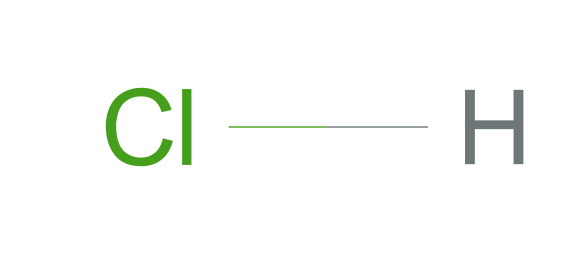
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
rxnPlt[rxn94["true rsmiles"],"True Reaction",rxn94["true rclass"]]
rxnPlt[rxn94["ret pred rsmiles"],"Retrosynthetic Prediction",rxn94["ret pred rclass"]]
rxnPlt[rxn94["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn94["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

## Sameness of Retrosynthetic and Forward Predictions (of true reactants)

```mathematica
(* 89 of the 98 have different retro and fwd reaction predictions *)
```

```mathematica
falseRetFwdPos=Position[Normal[allDatAnaly[[All,"ret and forward pred sameQ"]]],False];
```

```mathematica
(* This isn't overly surprising, just interesting to see if it would make the product the literature author thinks it should *)
```

## Reactions ΔSA > 0

### Retrosynthetic Prediction ΔSA > 0

```mathematica
Position[Normal@allDatAnaly,#]&/@Normal[allDatAnaly[Select[#"ret SA diff">0&]]]
```

{{{19}},{{78}},{{96}}}

#### Reaction #19

The reaction seems to be nonsensical. When I run this online it says it can’t find a synthetic route.

```mathematica
rxn18=allDatAnaly[Select[#"ret SA diff">0&]][[1]];
```

```mathematica
Framed@TableForm[{{rxn18["true SA diff"],rxn18["ret SA diff"],rxn18["canonical ret SA diff"],rxn18["forward pred SA diff"]}},TableHeadings->{{"ΔSA"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.20169 | 0.520332 | 0.520332 | 5.66694

```mathematica
rxnPlt[rxn18["true rsmiles"],"True Reaction",rxn18["true rclass"]]
rxnPlt[rxn18["ret pred rsmiles"],"Retrosynthetic Prediction",rxn18["ret pred rclass"]]
rxnPlt[rxn18["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn18["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #77

This was one of Nick’s reactions, I’m not sure if it’s “fair” or should be switched out. As far as a retrosynthesis, it just predicts a deprotonation, whereas the literature provides an actual synthesis.

```mathematica
rxn77=allDatAnaly[Select[#"ret SA diff">0&]][[2]];
```

```mathematica
Framed@TableForm[{{rxn77["true SA diff"],rxn77["ret SA diff"],rxn77["canonical ret SA diff"],rxn77["forward pred SA diff"]}},TableHeadings->{{"ΔSA"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -1.76506 | 0.790892 | 0.790892 | -2.55595

```mathematica
rxnPlt[rxn77["true rsmiles"],"True Reaction",rxn77["true rclass"]]
rxnPlt[rxn77["ret pred rsmiles"],"Retrosynthetic Prediction",rxn77["ret pred rclass"]]
rxnPlt[rxn77["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn77["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

rxnPlt[OCCC#Cc1ccccc1>>[O-]CCC#Cc1ccccc1,Canonical Retrosynthetic Prediction,payload[tree,rclass]]

#### Reaction #96

```mathematica
rxn95=allDatAnaly[Select[#"ret SA diff">0&]][[3]];
```

```mathematica
Position[Normal@allDatAnaly,Normal@rxn95]
```

{{96}}

```mathematica
Framed@TableForm[{{rxn95["true SA diff"],rxn95["ret SA diff"],rxn95["canonical ret SA diff"],rxn95["forward pred SA diff"]}},TableHeadings->{{"ΔSA"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -5.25234 | 1.338 | 1.338 | -6.25105

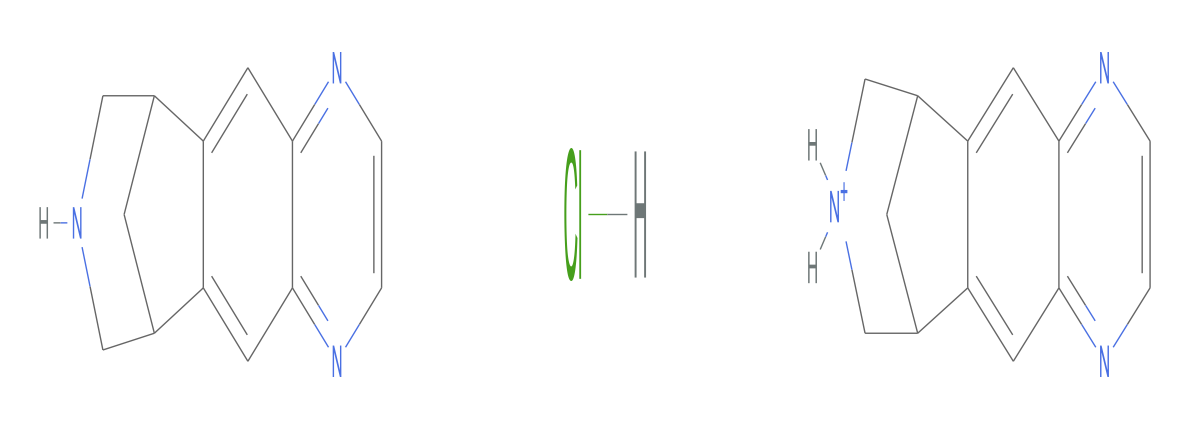

-Graphics-

rxnPlt[O=C(OCc1ccccc1)N1CC2CC(C1)c1cc3nccnc3cc12>>c1cnc2cc3c(cc2n1)C1C[NH2+]CC3C1,Canonical Retrosynthetic Prediction,payload[tree,rclass]]

```mathematica
rxnPlt[rxn95["true rsmiles"],"True Reaction",rxn95["true rclass"]]
rxnPlt[rxn95["ret pred rsmiles"],"Retrosynthetic Prediction",rxn95["ret pred rclass"]]
rxnPlt[rxn95["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn95["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

An acid hydrolysis of the amide?

### Forward ΔSA > 0

```mathematica
Position[Normal@allDatAnaly,#]&/@Normal[allDatAnaly[Select[#"forward pred SA diff">0&]]]
```

{{{19}}}

#### Reaction #19

```mathematica
Framed@TableForm[{{rxn18["true SA diff"],rxn18["ret SA diff"],rxn18["canonical ret SA diff"],rxn18["forward pred SA diff"]}},TableHeadings->{{"ΔSA"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.20169 | 0.520332 | 0.520332 | 5.66694

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn18
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.20169 | 0.520332 | 0.520332 | 5.66694
Conf | - | 0.0229 | 0.0229 | 0.0643187
Opt | - | 0.025 | 0.025 | -

```mathematica
rxnPlt[rxn18["true rsmiles"],"True Reaction",rxn18["true rclass"]]
rxnPlt[rxn18["ret pred rsmiles"],"Retrosynthetic Prediction",rxn18["ret pred rclass"]]
rxnPlt[rxn18["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",rxn18["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]
```

-Graphics-

-Graphics-

rxnPlt[O=C1CCCCC1>>C=C1CCCCC1,Canonical Retrosynthetic Prediction,payload[tree,rclass]]

## Reactions ΔCm > 0

### Retrosynthetic Prediction ΔCm > 0

```mathematica
Position[Normal@allDatAnaly,#]&/@Normal[allDatAnaly[Select[#"ret Cm diff">0&]]]
```

{{{2}},{{3}},{{4}},{{16}},{{18}},{{23}},{{27}},{{40}},{{42}},{{43}},{{45}},{{49}},{{60}},{{61}},{{68}},{{72}},{{76}},{{93}}}

### Forward ΔCm > 0

```mathematica
Position[Normal@allDatAnaly,#]&/@Normal[allDatAnaly[Select[#"forward pred Cm diff">0&]]]
```

{{{1}},{{3}},{{4}},{{5}},{{7}},{{8}},{{9}},{{10}},{{12}},{{16}},{{20}},{{21}},{{22}},{{23}},{{24}},{{27}},{{28}},{{31}},{{32}},{{34}},{{35}},{{39}},{{40}},{{41}},{{42}},{{43}},{{45}},{{47}},{{51}},{{54}},{{55}},{{56}},{{57}},{{60}},{{62}},{{63}},{{64}},{{65}},{{66}},{{67}},{{69}},{{70}},{{71}},{{72}},{{76}},{{78}},{{79}},{{82}},{{84}},{{86}},{{93}},{{95}},{{98}}}

## Reactions with ΔSA > 0 & ΔCm >0 (NONE)

```mathematica
allDatAnaly[Select[#"ret SA diff">0&&Select[#"ret Cm diff">0&]&]]
```

```mathematica
allDatAnaly[Select[#"forward pred SA diff">0&&Select[#"forward pred Cm diff">0&]&]]
```

## Reactions w/ Confidence < 0.1

```mathematica
lowConfRxns=allDatAnaly[Select[#"ret confidence"<0.1&]];
```

```mathematica
lowConfRxns//Length
```

9

```mathematica
GraphicsColumn[{rxnPlt[#["true rsmiles"],"Literature Reaction",#["true rclass"]],rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]],rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthesis Reaction",#["ret pred rclass"]]},ImageSize->Full]&/@Normal[allDatAnaly[Select[#"ret confidence"<0.1&]]];
```

```mathematica
Position[Normal@allDatAnaly,#]&/@Normal@lowConfRxns
```

{{{16}},{{19}},{{23}},{{68}},{{71}},{{72}},{{78}},{{96}},{{98}}}

#### Reaction #16 - Retrosynthesis ≠ Forward

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[1]]]
```

{{16}}

```mathematica
rxn16=lowConfRxns[[1]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn16
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -0.980856 | -12.0587 | -12.0587 | -0.980856
Conf | - | 0.000349 | 0.000349 | 0.178568
Opt | - | 0.000371 | 0.000371 | -

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn16
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn16
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn16
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn16["ret and canonical pred sameQ"]
```

True

```mathematica
rxn16retFwd=IBMRxn["new prediction",StringSplit[reacSplit[rxn16["ret pred rsmiles"]][[1]],"."],rxn16["project ID"],"dataset"];
```

```mathematica
sameRsmiles[StringRiffle[{rxn16retFwd["rreac"],rxn16retFwd["rprod"]},">>"],rxn16["ret pred rsmiles"]]
```

False

When the retrosynthesis products are fed through the forward prediction, products don’t match.

-Graphics-

-Graphics-

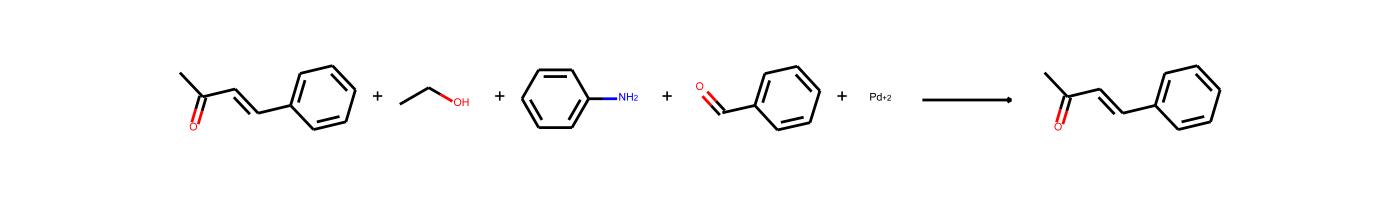

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn16
rxnPlt[StringRiffle[{rxn16retFwd["rreac"],rxn16retFwd["rprod"]},">>"],"Ret Fwd Reaction",""]
rxn16retFwd["reaction image"]
```

#### Reaction #19 - Retrosynthesis fails & gives 1 reactant

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[2]]]
```

{{19}}

```mathematica
rxn19=lowConfRxns[[2]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn19
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.20169 | 0.520332 | 0.520332 | 5.66694
Conf | - | 0.0229 | 0.0229 | 0.0643187
Opt | - | 0.025 | 0.025 | -

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn19
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn19
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn19
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn19["ret and canonical pred sameQ"]
```

True

This totally fails, you can’t supply a single reactant for a forward prediction.

#### Reaction #23 - Retrosynthesis ≠ Forward

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[3]]]
```

{{23}}

```mathematica
rxn23=lowConfRxns[[3]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn23
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.37895 | -6.71548 | -37.3618 | -2.09308
Conf | - | 0.00992 | 0.025 | 0.40316
Opt | - | 0.00849 | 0.0249 | -

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn23
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn23
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn23
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn23["ret and canonical pred sameQ"]
```

False

```mathematica
(* for the non-canonical ret pred: *)
```

```mathematica
rxn23retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn23;
```

```mathematica
sameRsmiles[StringRiffle[{rxn23retFwd["rreac"],rxn23retFwd["rprod"]},">>"],rxn23["ret pred rsmiles"]]
```

False

Forward prediction predicts bromine adding to the double bond rather than at the benzylic position predicted by the non-canonical retrosynthesis.

-Graphics-

-Graphics-

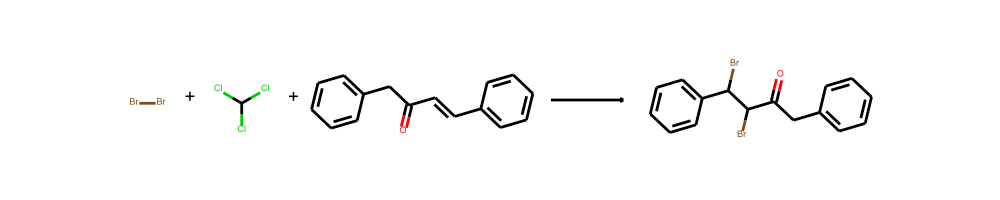

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn23
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"],"",""]&@rxn23retFwd
#["reaction image"]&@rxn23retFwd
```

```mathematica
(* for the canonical ret pred: *)
```

```mathematica
rxn23CretFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["canonical ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn23;
```

```mathematica
sameRsmiles[StringRiffle[{rxn23CretFwd["rreac"],rxn23CretFwd["rprod"]},">>"],rxn23["canonical ret pred rsmiles"]]
```

True

Prediction is the same for fwd and canonical ret pred.

-Graphics-

rxnPlt[CC(=O)C(Br)c1ccccc1.CCO.O=Cc1ccccc1.[Na+].[Na+].[OH-].[OH-]>>O=C(C=Cc1ccccc1)C(Br)c1ccccc1]

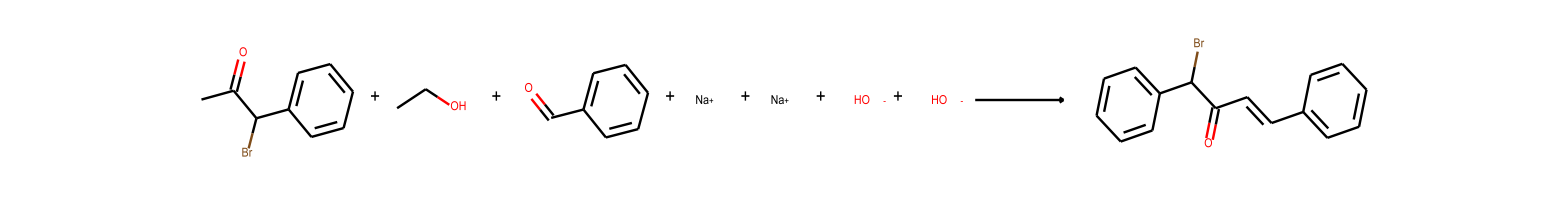

```mathematica
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthesis Reaction","canonical rlcass"]&@rxn23
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"]]&@rxn23CretFwd
#["reaction image"]&@rxn23CretFwd
```

#### Reaction #68 - Retrosynthesis ≠ Forward (Invalid rxn img)

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[4]]]
```

{{68}}

```mathematica
rxn68=lowConfRxns[[4]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn68
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -2.74671 | -4.00348 | -4.00348 | -3.68812
Conf | - | 0.00721 | 0.00721 | 0.527183
Opt | - | 0.00504 | 0.00504 | -

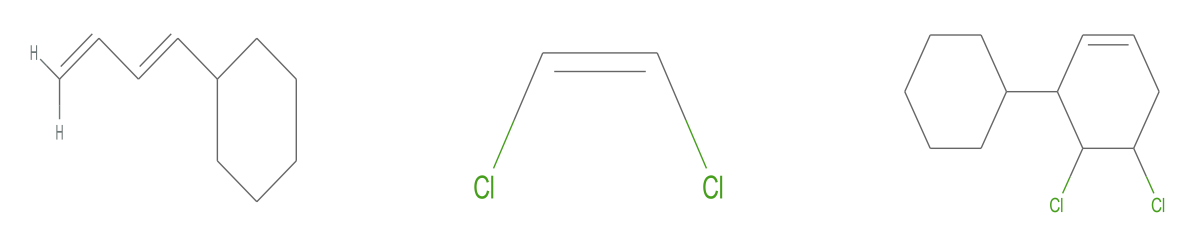

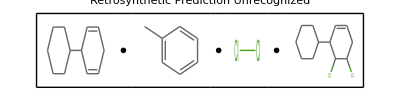

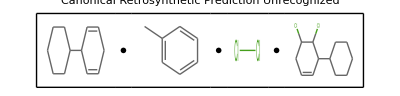

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn68
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn68
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn68
```

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn68["ret and canonical pred sameQ"]
```

True

```mathematica
rxn68retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn68;
```

```mathematica
sameRsmiles[StringRiffle[{rxn68retFwd["rreac"],rxn68retFwd["rprod"]},">>"],rxn16["ret pred rsmiles"]]
```

False

When the retrosynthesis products are fed through the forward prediction, products don’t match.

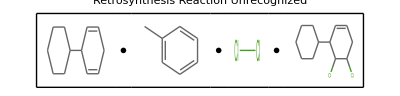

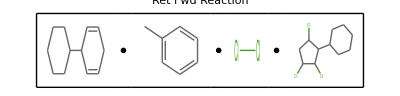

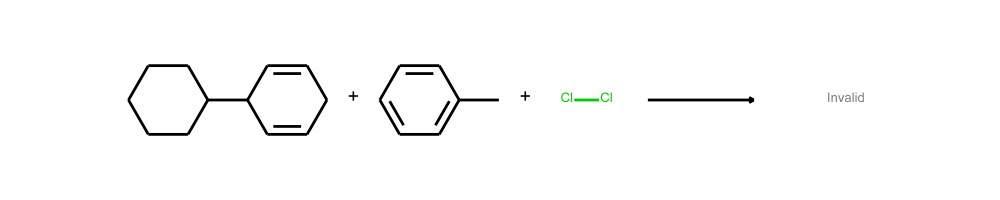

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn68
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"],"Ret Fwd Reaction",""]&@rxn68retFwd
#["reaction image"]&@rxn68retFwd
```

#### Reaction #71 - Retrosynthesis ≠ Forward (very strange prediction)

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[5]]]
```

{{71}}

```mathematica
rxn71=lowConfRxns[[5]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn71
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -4.37882 | -3.97472 | -3.97472 | -3.06527
Conf | - | 0.00283 | 0.00283 | 0.0511858
Opt | - | 0.00276 | 0.00276 | -

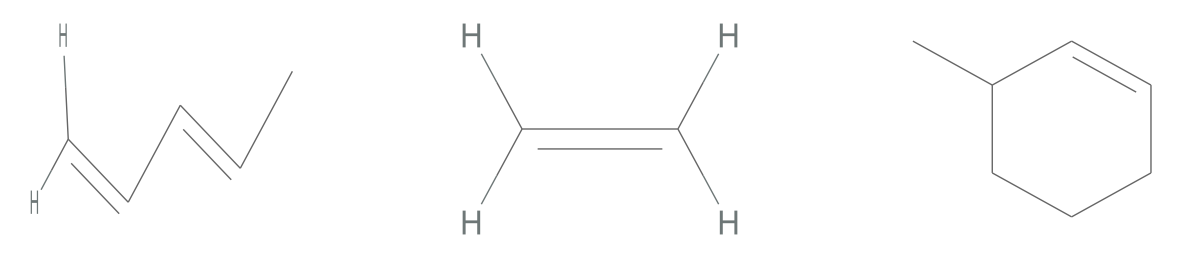

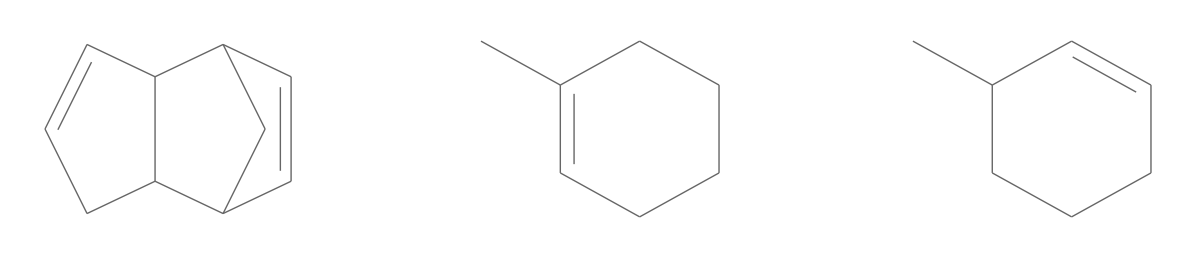

rxnPlt[C1=CC2C3C=CC(C3)C2C1.CC1=CCCCC1>>CC1C=CCCC1,Canonical Retrosynthetic Prediction,payload[tree,rclass]]

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn71
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn71
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn71
```

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn71["ret and canonical pred sameQ"]
```

True

```mathematica
rxn71retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn71;
```

StringJoin::string: String expected at position 2 in rxn.res.ibm.com/rxn/api/api/v1/predictions/<>Missing[KeyAbsent,payload].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[payload[name],_~~___→].

ResourceFunction::usermessage: SVGImport

Part::partw: Part 2 of reacSplit[payload[smiles]] does not exist.

```mathematica
sameRsmiles[StringRiffle[{rxn71retFwd["rreac"],rxn71retFwd["rprod"]},">>"],rxn71["ret pred rsmiles"]]
```

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

True

When the retrosynthesis products are fed through the forward prediction, products don’t match.

-Graphics-

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[payload[smiles]] is not a valid molecule.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[Part[reacSplit[payload[smiles]], 2]] is not a valid molecule.

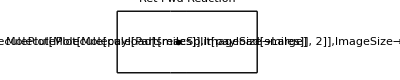

[◼] | SVGImport[payload[reactionImage]]

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn71
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"],"Ret Fwd Reaction",""]&@rxn71retFwd
#["reaction image"]&@rxn71retFwd
```

#### Reaction #72 - Retrosynthesis ≠ Forward (invalid rxn img)

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[6]]]
```

{{72}}

```mathematica
rxn72=lowConfRxns[[6]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn72
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -3.96934 | -1.53441 | -1.53441 | -3.44569
Conf | - | 0.000131 | 0.000131 | 0.137993
Opt | - | 0.000207 | 0.000207 | -

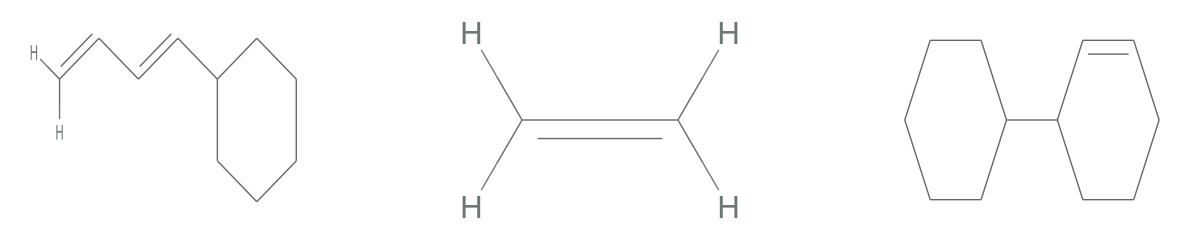

-Graphics-

-Graphics-

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn72
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn72
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn72
```

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn72["ret and canonical pred sameQ"]
```

True

```mathematica
rxn72retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn72;
```

```mathematica
sameRsmiles[StringRiffle[{rxn72retFwd["rreac"],rxn72retFwd["rprod"]},">>"],rxn72["ret pred rsmiles"]]
```

False

When the retrosynthesis products are fed through the forward prediction, products don’t match. Reaction image product is invalid.

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn72
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"],"Ret Fwd Reaction",""]&@rxn72retFwd
#["reaction image"]&@rxn72retFwd
```

-Graphics-

-Graphics-

-Graphics-

#### Reaction #78 - Gives 1 reactant (deprotonation) - maybe test with restricted SMs

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[7]]]
```

{{78}}

```mathematica
rxn78=lowConfRxns[[7]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn78
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -1.76506 | 0.790892 | 0.790892 | -2.55595
Conf | - | 0.000198 | 0.000198 | 0.336824
Opt | - | 0.000207 | 0.000207 | -

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn78
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn78
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn78
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn78["ret and canonical pred sameQ"]
```

True

```mathematica
rxn78retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn78;
```

StringJoin::string: String expected at position 2 in rxn.res.ibm.com/rxn/api/api/v1/predictions/<><|payload→Null,metadata→<|uiMessages→<|errors→{<|code→Null,«3»,target→TOAST|>},infos→{},warnings→{}|>,extendedPagination→<||>|>|>[payload,id].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[payload[name],_~~___→].

ResourceFunction::usermessage: SVGImport

Part::partw: Part 2 of reacSplit[payload[smiles]] does not exist.

```mathematica
sameRsmiles[StringRiffle[{rxn78retFwd["rreac"],rxn78retFwd["rprod"]},">>"],rxn78["ret pred rsmiles"]]
```

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

True

Fails bc predicts a single reactant.

```mathematica
(* test with restricted starting materials *)
```

#### Reaction #96 - Gives 1 reactant (amide hydrolysis in acidic conditions) - maybe test with restricted SMs

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[8]]]
```

{{96}}

```mathematica
rxn96=lowConfRxns[[8]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn96
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -5.25234 | 1.338 | 1.338 | -6.25105
Conf | - | 0.0000155 | 0.0000155 | 0.601838
Opt | - | 0.0000177 | 0.0000177 | -

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn96
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn96
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn96
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn96["ret and canonical pred sameQ"]
```

True

```mathematica
rxn96retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn96;
```

StringJoin::string: String expected at position 2 in rxn.res.ibm.com/rxn/api/api/v1/predictions/<>Missing[KeyAbsent,payload].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[payload[name],_~~___→].

ResourceFunction::usermessage: SVGImport

Part::partw: Part 2 of reacSplit[payload[smiles]] does not exist.

```mathematica
sameRsmiles[StringRiffle[{rxn96retFwd["rreac"],rxn96retFwd["rprod"]},">>"],rxn96["ret pred rsmiles"]]
```

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

True

Only one forward product is given.

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn96
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"],"Ret Fwd Reaction",""]&@rxn96retFwd
#["reaction image"]&@rxn96retFwd
```

-Graphics-

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[payload[smiles]] is not a valid molecule.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[Part[reacSplit[payload[smiles]], 2]] is not a valid molecule.

-Graphics-

[◼] | SVGImport[payload[reactionImage]]

#### Reaction #98 - # of Carbons is wrong

```mathematica
Position[Normal@allDatAnaly,Normal@lowConfRxns[[9]]]
```

{{98}}

```mathematica
rxn98=lowConfRxns[[9]];
```

```mathematica
Framed[TableForm[{{#["true SA diff"],#["ret SA diff"],#["canonical ret SA diff"],#["forward pred SA diff"]},{"-",#["ret confidence"],#["canonical ret confidence"],#["forward pred confidence"]},{"-",#["ret optimization"],#["canonical ret optimization"],-""}},TableHeadings->{{"ΔSA","Conf","Opt"},{"Literature","Retrosynthesis","Canonical\nRetrosynthesis","Forward"}}]]&@rxn98
```

| Literature | Retrosynthesis | Canonical
Retrosynthesis | Forward
ΔSA | -29.1149 | -15.4225 | -15.4225 | -28.6561
Conf | - | 0.0211 | 0.0211 | 0.908794
Opt | - | 0.0195 | 0.0195 | -

```mathematica
rxnPlt[#["true rsmiles"],"True Reaction",#["true rclass"]]&@rxn98
rxnPlt[#["ret pred rsmiles"],"Retrosynthetic Prediction",#["ret pred rclass"]]&@rxn98
rxnPlt[#["canonical ret pred rsmiles"],"Canonical Retrosynthetic Prediction",IBMRxn["recover retrosynthesis",#["canonical ret ID"],"dataset"][ReverseSortBy[#conf&]][[1]]["rclass"]]&@rxn98
```

-Graphics-

-Graphics-

rxnPlt[C#CCCCCCCC.N.[Na]>>C=CCCCCCC,Canonical Retrosynthetic Prediction,payload[tree,rclass]]

```mathematica
(* does the proposed forward reaction match/work? *)
```

```mathematica
rxn98["ret and canonical pred sameQ"]
```

True

```mathematica
rxn98retFwd=IBMRxn["new prediction",StringSplit[reacSplit[#["ret pred rsmiles"]][[1]],"."],#["project ID"],"dataset"]&@rxn98;
```

StringJoin::string: String expected at position 2 in rxn.res.ibm.com/rxn/api/api/v1/predictions/<>Missing[KeyAbsent,payload].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[payload[name],_~~___→].

ResourceFunction::usermessage: SVGImport

Part::partw: Part 2 of reacSplit[payload[smiles]] does not exist.

```mathematica
sameRsmiles[StringRiffle[{rxn98retFwd["rreac"],rxn98retFwd["rprod"]},">>"],rxn98["ret pred rsmiles"]]
```

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

True

Alchemy?

```mathematica
rxnPlt[#["ret pred rsmiles"],"Retrosynthesis Reaction",#["ret pred rclass"]]&@rxn98
rxnPlt[StringRiffle[{#["rreac"],#["rprod"]},">>"],"Ret Fwd Reaction",""]&@rxn98retFwd
#["reaction image"]&@rxn98retFwd
```

-Graphics-

Molecule::nintrp: Unable to interpret payload[smiles] as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[payload[smiles]] is not a valid molecule.

Molecule::nintrp: Unable to interpret Part[reacSplit[payload[smiles]], 2] as a name or chemical identifier.

MoleculePlot::mol: Argument Molecule[Part[reacSplit[payload[smiles]], 2]] is not a valid molecule.

-Graphics-

[◼] | SVGImport[payload[reactionImage]]

### What Kinds of Reactions are these?

```mathematica
tclasses=DeleteDuplicates[Normal[allDatAnaly[[All,"true rclass"]]]]
```

{electrophilic aromatic substitution,amide formation,epoxide opening,conjugate addition,dielsalder,robinson,cyclisation,elimination,substitution,friedelcrafts,nucleophilic aromatic substitution,grignard,organocopper,acetylide,e-sub,amine}

```mathematica
rGroups=Table[allDatAnaly[Select[#"true rclass"==tclasses[[i]]&]],{i,1,Length@tclasses}];
```

```mathematica
confs=If[Length[#]==1,First[#]["ret confidence"],Mean@Normal[#[[All,"ret confidence"]]]]&/@rGroups
```

{0.982,0.929,0.946,0.936,0.660288,0.84025,0.645783,0.588225,0.78888,0.922091,0.900667,0.9128,0.996,0.83615,0.794,0.660235}

```mathematica
AssociationThread[tclasses,confs]//Sort
```

<|elimination→0.588225,cyclisation→0.645783,amine→0.660235,dielsalder→0.660288,substitution→0.78888,e-sub→0.794,acetylide→0.83615,robinson→0.84025,nucleophilic aromatic substitution→0.900667,grignard→0.9128,friedelcrafts→0.922091,amide formation→0.929,conjugate addition→0.936,epoxide opening→0.946,electrophilic aromatic substitution→0.982,organocopper→0.996|>

```mathematica
BarChart[confs,ChartLabels->{"EAS","AF","EO","CA","DA","Ro","Cyc","EL","SUB","FC","NAS","Gr","OC","Acet","ESUB","Amine"}]
```

-Graphics-

## Do Different Retrosyntheses Make the Same Product? - Round Trip Analysis (formatting needs cleaning up)

### Get Fwd Predictions for Reasonable Other Retrosyntheses

Here I wanted to get retrosyntheses other than the original highest quality one, within reason. I chose to take unique (not the same reaction class) retrosynthetic predictions within a standard deviation of the mean confidence.

```mathematica
sameMolec[molec1_String,molec2_String]:=Module[{mol1=Molecule[molec1],mol2=Molecule[molec2],test},
test=Total[Boole[{MoleculeEquivalentQ[mol1,mol2],MoleculeEquivalentQ[Molecule[mol1["CanonicalSMILES"]],Molecule[mol2["CanonicalSMILES"]]],MoleculeEquivalentQ[Molecule[mol1["CanonicalSMILES"]],mol2],MoleculeEquivalentQ[mol1,Molecule[mol2["CanonicalSMILES"]]]}]];
If[test==0,False,True]
]
```

```mathematica
difRets[dat_]:=Module[{projID,rets,retsDel,confs,meanConf,stdConf,choiceRets,fwdPreds,retsLength},
projID=Normal[dat["project ID"]];
rets=IBMRxn["recover retrosynthesis",Normal[dat["ret ID"]],"dataset"];(* recovers ret to get alternative ret sequences *)
retsDel=Take[Dataset[DeleteDuplicatesBy[Normal[rets],#1["rclass"]==#2["rclass"]&]//Quiet],UpTo[5]];(* gets the top UpTo[5] unique rets, including the top conf *)
confs=Normal[retsDel[[All,"conf"]]];
meanConf=Mean[confs];
stdConf=StandardDeviation[confs];
choiceRets=retsDel[Select[#conf<(meanConf+stdConf)&&#conf>(meanConf-stdConf)&&#"rclass"≠dat["ret pred rclass"]&&(#"rreac"<>">>"<>#"prod")≠dat["ret pred rsmiles"]&&#"conf"≠dat["ret confidence"]&&#"opt"≠dat["ret optimization"]&]];
fwdPreds=ResourceFunction["MapBatched"][IBMRxn["new prediction",{#},projID,"dataset"]&,Normal[choiceRets[[All,"rreac"]]],Pause[15];,1];
retsLength=Length@choiceRets;

Dataset[<|
"reaction number"->dat["reaction number"],"true rclass"->dat["true rclass"],"true rsmiles"->dat["true rsmiles"],"true reacs"->dat["true reacs"],"true prod"->dat["true prod"],"notes"->dat["notes"],

"true SA diff"->dat["true SA diff"],
"true Cm diff"->dat["true Cm diff"],

"canonical true rsmiles"->dat["canonical true rsmiles"],"canonical true reacs"->dat["canonical true reacs"],"canonical true prod"->dat["canonical true prod"],

"canonical true SA diff"->dat["canonical true SA diff"],
"canonical true Cm diff"->dat["canonical true Cm diff"],

"project ID"->dat["project ID"],"ret ID"->dat["ret ID"],"ret pred rclass"->dat["ret pred rclass"],"ret pred rsmiles"->dat["ret pred rsmiles"],"ret pred reacs"->dat["ret pred reacs"],"ret confidence"->dat["ret confidence"],"ret optimization"->dat["ret optimization"],

"ret SA diff"->dat["ret SA diff"],
"ret Cm diff"->dat["ret Cm diff"],

"canonical ret ID"->dat["canonical ret ID"],"canonical ret pred rsmiles"->dat["canonical ret pred rsmiles"],"canonical ret pred reacs"->dat["canonical ret pred reacs"],"canonical ret confidence"->dat["canonical ret confidence"],"canonical ret optimization"->dat["canonical ret optimization"],

"canonical ret SA diff"->dat["canonical ret SA diff"],
"canonical ret Cm diff"->dat["canonical ret Cm diff"],

"forward pred ID"->dat["forward pred ID"],"forward pred rsmiles"->dat["forward pred rsmiles"],"forward pred reacs"->dat["forward pred reacs"],"forward pred prod"->dat["forward pred prod"],"forward pred confidence"->dat["forward pred confidence"],
"forward pred makes prod"->sameMolec[dat["true prod"],dat["forward pred prod"]],

"forward pred SA diff"->dat["forward pred SA diff"],
"forward pred Cm diff"->dat["forward pred Cm diff"],

"ret and canonical pred sameQ"->dat["ret and canonical pred sameQ"],
"ret and forward pred sameQ"->dat["ret and forward pred sameQ"],

"fwd 2 pred ID"->If[retsLength<1,"",fwdPreds[[1]]["predID"]],
"fwd 2 pred rsmiles"->If[retsLength<1,"",(fwdPreds[[1]]["rreac"]<>">>"<>fwdPreds[[1]]["rprod"])],"fwd 2 pred reacs"->If[retsLength<1,"",fwdPreds[[1]]["rreac"]],
"fwd 2 pred prod"->If[retsLength<1,"",fwdPreds[[1]]["rprod"]],"fwd 2 pred confidence"->If[retsLength<1,"",fwdPreds[[1]]["conf"]],"fwd 2 pred makes prod"->If[retsLength<1,"",sameMolec[dat["true prod"],fwdPreds[[1]]["rprod"]]],

"fwd 3 pred ID"->If[retsLength<2,"",fwdPreds[[2]]["predID"]],"fwd 3 pred rsmiles"->If[retsLength<2,"",fwdPreds[[2]]["rreac"]<>">>"<>fwdPreds[[2]]["rprod"]],"fwd 3 pred reacs"->If[retsLength<2,"",fwdPreds[[2]]["rreac"]],
"fwd 3 pred prod"->If[retsLength<2,"",fwdPreds[[2]]["rprod"]],
"fwd 3 pred confidence"->If[retsLength<2,"",fwdPreds[[2]]["conf"]],"fwd 3 pred makes prod"->If[retsLength<2,"",sameMolec[dat["true prod"],fwdPreds[[2]]["rprod"]]],

"fwd 4 pred ID"->If[retsLength<3,"",fwdPreds[[3]]["predID"]],"fwd 4 pred rsmiles"->If[retsLength<3,"",fwdPreds[[3]]["rreac"]<>">>"<>fwdPreds[[3]]["rprod"]],"fwd 4 pred reacs"->If[retsLength<3,"",fwdPreds[[3]]["rreac"]],
"fwd 4 pred prod"->If[retsLength<3,"",fwdPreds[[3]]["rprod"]],
"fwd 4 pred confidence"->If[retsLength<3,"",fwdPreds[[3]]["conf"]],"fwd 4 pred makes prod"->If[retsLength<3,"",sameMolec[dat["true prod"],fwdPreds[[3]]["rprod"]]],

"fwd 5 pred ID"->If[retsLength<4,"",fwdPreds[[4]]["predID"]],"fwd 5 pred rsmiles"->If[retsLength<4,"",(fwdPreds[[4]]["rreac"]<>">>"<>fwdPreds[[4]]["rprod"])],"fwd 5 pred reacs"->If[retsLength<4,"",fwdPreds[[4]]["rreac"]],
"fwd 5 pred prod"->If[retsLength<4,"",fwdPreds[[4]]["rprod"]],
"fwd 5 pred confidence"->If[retsLength<4,"",fwdPreds[[4]]["conf"]],"fwd 5 pred makes prod"->If[retsLength<4,"",sameMolec[dat["true prod"],fwdPreds[[4]]["rprod"]]]
|>]
]
```

```mathematica
(* let's first retrieve all of the requisite choiceRets *)
```

```mathematica
getChoiceRets[dat_]:=Module[{projID,rNumber,trSmiles,treacs,tprod,rets,retsDel,confs,meanConf,stdConf,choiceRets},
projID=Normal[dat["project ID"]];
rNumber=Normal[dat["reaction number"]];
trSmiles=Normal[dat["true rsmiles"]];
treacs=Normal[dat["true reacs"]];
tprod=Normal[dat["true prod"]];

rets=IBMRxn["recover retrosynthesis",Normal[dat["ret ID"]],"dataset"];(* recovers ret to get alternative ret sequences *)
retsDel=If[
SameQ[First[DeleteDuplicates[Normal[rets[[All,"rclass"]]]]],"Unrecognized"],Take[Dataset[DeleteDuplicatesBy[Normal[rets],#1["rreac"]==#2["rreac"]&]//Quiet],UpTo[5]],
Take[Dataset[DeleteDuplicatesBy[Normal[rets],#1["rclass"]==#2["rclass"]&]//Quiet],UpTo[5]]
];(* gets the top UpTo[5] unique rets, including the top conf *)
confs=Normal[retsDel[[All,"conf"]]];
meanConf=Mean[confs];
stdConf=If[Length[confs]==1,1,StandardDeviation[confs]];
choiceRets=retsDel[Select[#conf<(meanConf+stdConf)&&#conf>(meanConf-stdConf)&&#"rclass"≠dat["ret pred rclass"]&&(#"rreac"<>">>"<>#"prod")≠dat["ret pred rsmiles"]&]];
choiceRets[All,Prepend[#,Join[<|"reaction number"->rNumber,"true rsmiles"->trSmiles,"true reacs"->treacs,"tprod"->tprod|>]]&]
]
```

Here, I ended up having to repeat these analyses for two sets of data, the reactions that were originally picked and then for some “left out” reactions, which were left out due to an error in my initial getChoiceRets[] function. Note that the variables ending in or including LO are the same operations, just done on the reactions that got “left out” from the original grouping.

To generate choiceRets, I am mapping over all of the reactions in the dataset, getting the alternative retrosyntheses for each example, and choosing up to 5 unique rclass retrosyntheses, not including the original highest confidence retrosynthesis. From these, I’m only taking those within a standard deviation of the total confidence mean, to not bias this metric with uncharacteristically low confidence predictions. choiceRets is grouped by each reaction, choiceRetsFlat just flattens it out into a smooth dataset.

```mathematica
(*choiceRets=ResourceFunction["MapBatched"][getChoiceRets[#]&,allDatAnaly,Pause[15];,1];
```

```mathematica
(*Dataset@Flatten@Normal@Normal@choiceRets//Length
```

```mathematica
(*choiceRetsFlat=Dataset@Flatten@Normal@Normal@choiceRets;(* flattened dataset of all of the chosen alternative retrosyntheses *)
```

```mathematica
choiceRetsFlat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\choiceRetsFlat98.csv",HeaderLines->1];
```

```mathematica
(* add the left out rxns to choice rets flat *)
```

```mathematica
(*choiceRetsLO=ResourceFunction["MapBatched"][getChoiceRets[#]&,leftOutRxns,Pause[15];,1];
```

```mathematica
(*choiceRetsLOflat=Dataset[Flatten@Normal@Normal@choiceRetsLO];
```

```mathematica
getFwdPred[dat_]:=Module[{projID,fwdPred},
projID=dat["projID"];
fwdPred=If[
Length[StringSplit[dat["rreac"],"."]]==1,
Dataset[<|"project name"->"","projID"->projID,"predID"->"","rreac"->"","rprod"->"","conf"->"","reaction image"->""|>],
IBMRxn["new prediction",{dat["rreac"]},projID,"dataset"]];
Pause[15];
Dataset[<|
"reaction number"->Normal[dat["reaction number"]],"true rsmiles"->Normal[dat["true rsmiles"]],"true reacs"->Normal[dat["true reacs"]],"tprod"->Normal[dat["tprod"]],"rclass"->Normal[dat["rclass"]],"retroID"->Normal[dat["retroID"]],"ret rreac"->Normal[dat["rreac"]],"ret prod"->Normal[dat["prod"]],"ret confidence"->Normal[dat["conf"]],"ret optimization"->Normal[dat["opt"]],"project name"->Normal[fwdPred["project name"]],"projID"->Normal[fwdPred["projID"]],"fwd pred rsmiles"->(Normal[fwdPred["rreac"]]<>">>"<>Normal[fwdPred["rprod"]]),"fwd pred reacs"->Normal[fwdPred["rreac"]],"fwd pred prod"->Normal[fwdPred["rprod"]],"fwd pred conf"->Normal[fwdPred["conf"]],"fwd pred rxn img"->Normal[fwdPred["reaction image"]]
|>]
]
```

Here, I’m getting the forward prediction for each of the alternative retrosynthetic sequences, and formatting the dataset.

```mathematica
(*choiceRetsFlat[Select[Length[StringSplit[#rreac,"."]]==1&]];(* alternative rets with only one reactant given - are left blank *)
```

```mathematica
(*fwdPreds=ResourceFunction["MapBatched"][getFwdPred[#]&,choiceRetsFlat,Pause[65];,6];
```

```mathematica
(*fwdPredsFlat=Dataset@Normal@Normal@fwdPreds;
```

```mathematica
fwdPredsLO=ResourceFunction["MapBatched"][getFwdPred[#]&,choiceRetsLOflat,Pause[65];,6];
```

```mathematica
fwdPredsFlatLO=Dataset@Normal@Normal@fwdPredsLO;
```

```mathematica
fwdPredsFlat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\fwdPredsFlat98.csv",HeaderLines->1];
```

```mathematica
fwdPredsFlat//Length
```

126

```mathematica
fwdPredsFlat=Join[fwdPredsFlat,fwdPredsFlatLO];
```

```mathematica
Export["fwdPredsFlat98.csv",fwdPredsFlat]
```

fwdPredsFlat98.csv

```mathematica
(* let's include the original retrosynthesis and forward predictions too *)
```

```mathematica
allDatAnaly//First//Keys//Normal
```

{reaction number,true rclass,true rsmiles,true reacs,true prod,notes,true SA diff,true Cm diff,canonical true rsmiles,canonical true reacs,canonical true prod,canonical true SA diff,canonical true Cm diff,project ID,ret ID,ret pred rclass,ret pred rsmiles,ret pred reacs,ret confidence,ret optimization,ret SA diff,ret Cm diff,canonical ret ID,canonical ret pred rsmiles,canonical ret pred reacs,canonical ret confidence,canonical ret optimization,canonical ret SA diff,canonical ret Cm diff,forward pred ID,forward pred rsmiles,forward pred reacs,forward pred prod,forward pred confidence,forward pred SA diff,forward pred Cm diff,ret and canonical pred sameQ,ret and forward pred sameQ}

```mathematica
fwdPredsFlat//First//Keys//Normal
```

{reaction number,true rsmiles,true reacs,tprod,rclass,retroID,ret rreac,ret prod,ret confidence,ret optimization,project name,projID,fwd pred rsmiles,fwd pred reacs,fwd pred prod,fwd pred conf,fwd pred rxn img}

```mathematica
(* gets original retrosynthetic prediction and adds it to each group *)
```

```mathematica
getOrig[dat_]:=Module[{origDat,pred,origDatForm},
origDat=First[allDatAnaly[Select[#"true prod"==Normal[dat["tprod"]]&]]];
pred=If[
Length[StringSplit[origDat["ret pred reacs"],"."]]==1,
Dataset[<|"project name"->"","projID"->Normal[origDat["project ID"]],"predID"->"","rreac"->"","rprod"->"","conf"->"","reaction image"->""|>],IBMRxn["new prediction",StringSplit[Normal[origDat["ret pred reacs"]],"."],Normal[origDat["project ID"]],"dataset"]];
Pause[15];
origDatForm=Dataset[<|
"reaction number"->Normal[dat["reaction number"]],"true rsmiles"->Normal[dat["true rsmiles"]],"true reacs"->Normal[dat["true reacs"]],"tprod"->Normal[dat["tprod"]],"rclass"->"","retroID"->Normal[origDat["ret ID"]],"ret rreac"->Normal[origDat["ret pred reacs"]],"ret prod"->StringSplit[Normal[origDat["ret pred rsmiles"]],">>"][[2]],"ret confidence"->Normal[origDat["ret confidence"]],"ret optimization"->Normal[origDat["ret optimization"]],"project name"->"","projID"->Normal[origDat["project ID"]],"fwd pred rsmiles"->
(Normal[pred["rreac"]]<>">>"<>Normal[pred["rprod"]]),"fwd pred reacs"->Normal[pred["rreac"]],"fwd pred prod"->Normal[pred["rprod"]],"fwd pred conf"->Normal[pred["conf"]],"fwd pred rxn img"->pred["reaction image"]|>];
Pause[20];
origDatForm
]
```

Here I wanted to add the original, highest confidence retrosynthesis to each of the groups, because they were originally excluded to make sure we’re not double counting. pAndRSmiles gathers the unique {true product, true reaction smiles} to function as unique identifiers for each reaction group.

```mathematica
pAndRsmiles=DeleteDuplicates[Thread[{Normal[fwdPredsFlat[[All,"tprod"]]],Normal[fwdPredsFlat[[All,"true rsmiles"]]]}]];
```

```mathematica
pAndRsmilesLO=DeleteDuplicates[Thread[{Normal[fwdPredsFlatLO[[All,"tprod"]]],Normal[fwdPredsFlatLO[[All,"true rsmiles"]]]}]];
```

I use these unique identifiers to take the first entry from each group to allow querying in the original allDatAnaly dataset.

```mathematica
oneFromEach=DeleteDuplicates[fwdPredsFlat,((#1["tprod"]==#2["tprod"])&&(#1["true rsmiles"]==#2["true rsmiles"]))&];
```

```mathematica
oneFromEachLO=DeleteDuplicates[fwdPredsFlatLO,((#1["tprod"]==#2["tprod"])&&(#1["true rsmiles"]==#2["true rsmiles"]))&];
```

```mathematica
(* This is used to combined the groups of retrosyntheses with the original reaction and retrosynthesis from allDatAnaly *)
```

```mathematica
combine[uniqDat_,allDat_]:=(
Dataset@Flatten@Normal@{getOrig[uniqDat],allDat[Select[#"tprod"==Normal[uniqDat["tprod"]]&&#"true rsmiles"==Normal[uniqDat["true rsmiles"]]&]]}
)
```

The combinedDat is all of these extended retrosynthetic predictions with the original sequence added too.

```mathematica
(*combinedDat=ResourceFunction["MapBatched"][combine[#,fwdPredsFlat]&,oneFromEach,Pause[65];,6];
```

```mathematica
(*combinedDatflat=Dataset@Flatten@Normal@Normal[combinedDat];
```

```mathematica
(*combinedDatflat//First//Keys//Normal
```

```mathematica
combinedDatflat=SemanticImport["C:\\Users\\willr\\Desktop\\SchrierRsrch\\IBMRxn\\retro\\combDatFlat98.csv",HeaderLines->1];
```

```mathematica
combinedDatLO=ResourceFunction["MapBatched"][combine[#,fwdPredsFlatLO]&,oneFromEachLO,Pause[65];,6];
```

```mathematica
combinedDatFlatLO=Dataset[Flatten@Normal@Normal@combinedDatLO];
```

```mathematica
combDatFltAll=Join[combinedDatflat,combinedDatFlatLO];
```

Originally, only 77 unique options were included, indicating that some are missing.

```mathematica
(First[#]&/@combinedDatflat[GroupBy[#"true reacs"&]])[[Values,All]]//Length
```

77

```mathematica
leftOut=Complement[Normal[allDatAnaly[[All,"true rsmiles"]]],Normal[(First[#]&/@combinedDatflat[GroupBy[#"true reacs"&]])[[Values,All]][[All,"true rsmiles"]]]];
```

After fixing the problem we still have some missing (~15 rxn). Investigation showed these are a mixture of reactions that fail, only produce one retrosynthetic path type, or don’t have more than one sequence within a reasonable confidence boundary to the mean. These are hence considered failures in the round trip.

```mathematica
leftOutRxns=Dataset[Flatten@Normal[Table[allDatAnaly[Select[#"true rsmiles"==leftOut[[i]]&]],{i,1,21}]]];
```

```mathematica
(First[#]&/@combDatFltAll[GroupBy[#"true reacs"&]])[[Values,All]]//Length
```

83

### Round Trip Analysis

#### For All Reasonable Rets

Here we can compute the round trip (amount of alternative rclass retrosyntheses that produce the same product).

```mathematica
(* get these false examples *)
```

```mathematica
falsePos=Position[Quiet@MapThread[sameMolec[#1,#2]&,{Normal[combinedDatflat[[All,"tprod"]]],Normal[combinedDatflat[[All,"fwd pred prod"]]]}],False]
```

{{7},{12},{15},{17},{18},{23},{27},{29},{30},{45},{47},{48},{49},{51},{54},{55},{67},{80},{88},{91},{102},{103},{104},{105},{106},{107},{108},{109},{113},{114},{116},{120},{127},{135},{136},{138},{140},{144},{145},{146},{148},{149},{150},{156},{160},{161},{162},{163},{164},{165},{168},{169},{171},{173},{174},{176},{177},{178},{186},{187},{189},{198},{199},{202},{203}}

For taking all reasonable retrosyntheses (not only the highets confidence sequence) we get a round trip of ~68%. This is reasonable compared to the cited percentage ranging from 71.1% - 81.2%.

```mathematica
((Length[combinedDatflat]-Length[falsePos])/Length[combinedDatflat])*100//N
```

67.9803

```mathematica
(* For the updated list: *)
```

```mathematica
falsePosv2=Position[Quiet@MapThread[sameMolec[#1,#2]&,{Normal[combDatFltAll[[All,"tprod"]]],Normal[combDatFltAll[[All,"fwd pred prod"]]]}],False]
```

{{7},{12},{15},{17},{18},{23},{27},{29},{30},{45},{47},{48},{49},{51},{54},{55},{67},{80},{88},{91},{102},{103},{104},{105},{106},{107},{108},{109},{113},{114},{116},{120},{127},{135},{136},{138},{140},{144},{145},{146},{148},{149},{150},{156},{160},{161},{162},{163},{164},{165},{168},{169},{171},{173},{174},{176},{177},{178},{186},{187},{189},{198},{199},{202},{203}}

This round trip is made slightly better by including more of the examples (including the accidentally left out). This value is again very reasonable compared to what is cited in the paper.

```mathematica
((Length[combDatFltAll]-Length[falsePosv2])/Length[combDatFltAll])*100//N
```

70.7207

```mathematica
(* for computing the percent of reactions that made the correct product *)
```

```mathematica
corPct[uniqDat_,allDat_]:=Module[{grp,length,sameProd,numCor},
grp=allDat[Select[#"tprod"==Normal[uniqDat["tprod"]]&&#"true rsmiles"==Normal[uniqDat["true rsmiles"]]&]];
length=Length@grp;
sameProd=Quiet@Map[sameMolec[Normal[uniqDat["tprod"]],#]&,Normal[grp[[All,"fwd pred prod"]]]];
numCor=Length@Flatten@Position[sameProd,True];
(numCor/length)*100
]
```

```mathematica
percCor=Normal[Map[corPct[#,combinedDatflat]&,oneFromEach]];
```

```mathematica
{Histogram[percCor,{15},PlotTheme->{"Scientific","CoolColor"},PlotLabel->"% of Rets that Make Product in a Group",ImageSize->Large],Framed@TableForm[Table[{N@Mean[i],Median[i],N@StandardDeviation[i],N@Variance[i],Min[i],Max[i]},{i,{percCor}}],TableHeadings->{{},{"Mean","Median","Standard Deviation","Variance","Min","Max"}}]}
```

{-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
 | 67.8571 | 75 | 35.0885 | 1231.2 | 0 | 100}

```mathematica
(* updated *)
```

```mathematica
percCorv2=Normal[Map[corPct[#,combDatFltAll]&,Join[oneFromEach,oneFromEachLO]]];
```

```mathematica
{Histogram[percCorv2,{15},PlotTheme->{"Scientific","CoolColor"},PlotLabel->"% of Rets that Make Product in a Group",ImageSize->Large],Framed@TableForm[Table[{N@Mean[i],Median[i],N@StandardDeviation[i],N@Variance[i],Min[i],Max[i]},{i,{percCorv2}}],TableHeadings->{{},{"Mean","Median","Standard Deviation","Variance","Min","Max"}}]}
```

{-Graphics-, | Mean | Median | Standard Deviation | Variance | Min | Max
 | 70.1807 | 100 | 34.803 | 1211.25 | 0 | 100}

```mathematica
(* How many have at least one correct? *)
```

```mathematica
(Length[Select[percCor,#≠0&]]/Length[percCor])*100//N
```

88.3117

```mathematica
(* updated - how many have at least one correct - kinda coverage *)
```

```mathematica
(Length[Select[percCorv2,#≠0&]]/Length[percCorv2])*100//N
```

89.1566

```mathematica
pltProds[index_Integer,allDat_]:=Module[{group,numb},
group=allDat[Select[#"tprod"==Normal[allDat[[index]]["tprod"]]&&#"true rsmiles"==Normal[allDat[[index]]["true rsmiles"]]&]];
numb=Length@group;
Flatten@Append[{MoleculePlot[Molecule[First@DeleteDuplicates@Normal[group[[All,"tprod"]]]],PlotLabel->"Target Product",ImageSize->Medium]},Table[{MoleculePlot[Molecule@Normal[group[[All,"fwd pred prod"]]][[i]],PlotLabel->"Ret Fwd Prod "<>ToString[i]<>"\n"<>ToString[sameMolec[First@DeleteDuplicates@Normal[group[[All,"tprod"]]],Normal[group[[All,"fwd pred prod"]]][[i]]]],ImageSize->Medium]},{i,1,Length@group}]]
]
```

#### For 1st Ret (Highest Confidence)

```mathematica
(* How many first rets are correct? *)
```

```mathematica
allDatAnaly//First//Keys//Normal
```

{reaction number,true rclass,true rsmiles,true reacs,true prod,notes,true SA diff,true Cm diff,canonical true rsmiles,canonical true reacs,canonical true prod,canonical true SA diff,canonical true Cm diff,project ID,ret ID,ret pred rclass,ret pred rsmiles,ret pred reacs,ret confidence,ret optimization,ret SA diff,ret Cm diff,canonical ret ID,canonical ret pred rsmiles,canonical ret pred reacs,canonical ret confidence,canonical ret optimization,canonical ret SA diff,canonical ret Cm diff,forward pred ID,forward pred rsmiles,forward pred reacs,forward pred prod,forward pred confidence,forward pred SA diff,forward pred Cm diff,ret and canonical pred sameQ,ret and forward pred sameQ}

```mathematica
combinedDatflat//First//Keys//Normal
```

{reaction number,true rsmiles,true reacs,tprod,rclass,retroID,ret rreac,ret prod,ret confidence,ret optimization,project name,projID,fwd pred rsmiles,fwd pred reacs,fwd pred prod,fwd pred conf,fwd pred rxn img}

```mathematica
(* I think I'm missing a few reactions from the original test set *)
```

```mathematica
falsePosF=Position[Quiet@MapThread[sameMolec[#1,#2]&,{Normal[(First[#]&/@combinedDatflat[GroupBy[#"true reacs"&]])[[Values,All]][[All,"tprod"]]],Normal[(First[#]&/@combinedDatflat[GroupBy[#"true reacs"&]])[[Values,All]][[All,"fwd pred prod"]]]}],False]
```

{{18},{21},{36},{40},{41},{56},{58},{63},{75},{77}}

```mathematica
((Length[combinedDatflat]-Length[falsePosF])/Length[combinedDatflat])*100//N
```

95.0739

```mathematica
(* out of n=77 rxns *)
```

```mathematica
{{"Top 1 RT","Top Reasonable RT","Top Reasonable Coverage"},{((Length[combinedDatflat]-Length[falsePosF])/Length[combinedDatflat])*100//N,((Length[combinedDatflat]-Length[falsePos])/Length[combinedDatflat])*100//N,(Length[Select[percCor,#≠0&]]/Length[percCor])*100//N}}//TableForm
```

Top 1 RT | Top Reasonable RT | Top Reasonable Coverage
95.0739 | 67.9803 | 88.3117

```mathematica
(* updated with 'all' rxns *)
```

```mathematica
falsePosFv2=Position[Quiet@MapThread[sameMolec[#1,#2]&,{Normal[(First[#]&/@combDatFltAll[GroupBy[#"true reacs"&]])[[Values,All]][[All,"tprod"]]],Normal[(First[#]&/@combDatFltAll[GroupBy[#"true reacs"&]])[[Values,All]][[All,"fwd pred prod"]]]}],False]
```

{{18},{21},{36},{40},{41},{56},{58},{63},{75},{77}}

```mathematica
((Length[combDatFltAll]-Length[falsePosFv2])/Length[combDatFltAll])*100//N
```

95.4955

Round trip and coverage scores are all comparable to what is cited in the paper.

```mathematica
{{"Top 1 RT","Top Reasonable RT","Top Reasonable Coverage"},{((Length[combDatFltAll]-Length[falsePosFv2])/Length[combDatFltAll])*100//N,((Length[combDatFltAll]-Length[falsePosv2])/Length[combDatFltAll])*100//N,(Length[Select[percCorv2,#≠0&]]/Length[percCorv2])*100//N}}//TableForm
```

Top 1 RT | Top Reasonable RT | Top Reasonable Coverage
95.4955 | 70.7207 | 89.1566

## ISMI (Invalid SMILES Percent)

```mathematica
(* how many give invalid SMILES (ismi %) *)
```

Testing invalid smiles percent by seeing what SMILES entries don’t produce a valid molecule. 0% is reasonable given what is cited in the paper.

```mathematica
Table[Not@MemberQ[Map[Quiet@MoleculeQ[Molecule[#]]&,StringSplit[Normal[allDatAnaly[[All,"ret pred rsmiles"]]],{">>","."}][[i]]],False],{i,1,Length@allDatAnaly}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* What about for all reasonable rets *)
```

```mathematica
combinedDatflat//First//Keys//Normal
```

{reaction number,true rsmiles,true reacs,tprod,rclass,retroID,ret rreac,ret prod,ret confidence,ret optimization,project name,projID,fwd pred rsmiles,fwd pred reacs,fwd pred prod,fwd pred conf,fwd pred rxn img}

```mathematica
Table[Not@MemberQ[Map[Quiet@MoleculeQ[Molecule[#]]&,Flatten[StringSplit[{combinedDatflat[[i]]["ret rreac"],combinedDatflat[[i]]["ret prod"]},"."]]],False],{i,1,Length@combinedDatflat}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* for fwd *)
```

```mathematica
Table[Not@MemberQ[Map[Quiet@MoleculeQ[Molecule[#]]&,StringSplit[Normal[combinedDatflat[[All,"fwd pred rsmiles"]]],{">>","."}][[i]]],False],{i,1,Length@combinedDatflat}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}